# Konishi (and family) from slope-to-slope

## Basso’s slope and conjecture

Basso’s slope, its expansion gives all A_i coefficients:

```mathematica
slopesrs=Series[Series[1+(√λ)/J BesselI[J+1,√λ]/BesselI[J,√λ],{λ,∞,10}]/.Exp[a_ √λ]->Λ^a//Normal,{Λ,∞,0},{λ,∞,12}];
```

```mathematica
As=Table[A[i+2]->Simplify[2J SeriesCoefficient[Normal@slopesrs,{λ,∞,i/2}]],{i,-1,5}];
```

```mathematica
As//TableForm
```

A[1]→2
A[2]→-1
A[3]→-1/4+J^2
A[4]→-1/4+J^2
A[5]→1/64 (-25+104 J^2-16 J^4)
A[6]→-13/16+(7 J^2)/2-J^4
A[7]→1/512 (-1073+4748 J^2-1840 J^4+64 J^6)

The conjecture for the form of Δ^2:

```mathematica
Δsq=J^2+S(∑_(i=1)^7 A[i] λ^((2-i)/2))+S^2(∑_(i=1)^8 B[i] λ^((1-i)/2))+S^3(∑_(i=1)^8 CC[i] λ^((0-i)/2))+S^4(∑_(i=1)^8 DD[i] λ^((-1-i)/2))+S^5(∑_(i=1)^8 EE[i] λ^((-2-i)/2))+0 S^6(∑_(i=1)^8 FF[i] λ^((-3-i)/2))
```

S ((A(5))/λ^(3/2)+(A(7))/λ^(5/2)+(A(6))/λ^2+A(1) √λ+(A(3))/(√λ)+(A(4))/λ+A(2))+S^2 ((B(4))/λ^(3/2)+(B(6))/λ^(5/2)+(B(8))/λ^(7/2)+(B(7))/λ^3+(B(5))/λ^2+(B(2))/(√λ)+(B(3))/λ+B(1))+S^3 ((CC(3))/λ^(3/2)+(CC(5))/λ^(5/2)+(CC(7))/λ^(7/2)+(CC(8))/λ^4+(CC(6))/λ^3+(CC(4))/λ^2+(CC(1))/(√λ)+(CC(2))/λ)+S^4 ((DD(2))/λ^(3/2)+(DD(4))/λ^(5/2)+(DD(6))/λ^(7/2)+(DD(8))/λ^(9/2)+(DD(7))/λ^4+(DD(5))/λ^3+(DD(3))/λ^2+(DD(1))/λ)+S^5 ((EE(1))/λ^(3/2)+(EE(3))/λ^(5/2)+(EE(5))/λ^(7/2)+(EE(7))/λ^(9/2)+(EE(8))/λ^5+(EE(6))/λ^4+(EE(4))/λ^3+(EE(2))/λ^2)+J^2

And thus the reexpansion for the energy:

```mathematica
Δ=Series[√Δsq,{λ,∞,2}]//Simplify//Normal//#/.(1/λ)^(9/4)->0&//Series[#,{λ,∞,2}]&
```

λ^(1/4) √(A(1) S)+((1/λ)^(1/4) (S (A(2)+B(1) S)+J^2))/(2 √(A(1) S))-((1/λ)^(3/4) (√(A(1) S) ((S (A(2)+B(1) S)+J^2)^2-4 A(1) S^2 (A(3)+S (B(2)+CC(1) S)))))/(8 ((A(1))^2 S^2))+((1/λ)^(5/4) (2 S (A(4)+S (B(3)+S (CC(2)+DD(1) S)))+((S (A(2)+B(1) S)+J^2) ((S (A(2)+B(1) S)+J^2)^2-4 A(1) S^2 (A(3)+S (B(2)+CC(1) S))))/(4 (A(1))^2 S^2)))/(4 √(A(1) S))+1/(32 (A(1))^2 S^2)(1/λ)^(7/4) √(A(1) S) (16 A(1) S^2 (A(5)+S (B(4)+S (CC(3)+S (DD(2)+EE(1) S))))-5 (S (A(2)+B(1) S)+J^2) (2 S (A(4)+S (B(3)+S (CC(2)+DD(1) S)))+((S (A(2)+B(1) S)+J^2) ((S (A(2)+B(1) S)+J^2)^2-4 A(1) S^2 (A(3)+S (B(2)+CC(1) S))))/(4 (A(1))^2 S^2))+2 S (S (A(2)+B(1) S)+J^2) (A(4)+S (B(3)+S (CC(2)+DD(1) S)))+((A(3)+S (B(2)+CC(1) S)) ((S (A(2)+B(1) S)+J^2)^2-4 A(1) S^2 (A(3)+S (B(2)+CC(1) S))))/(A(1)))+O((1/λ)^(9/4))

Which coefficients do we need for 3 loops ?

```mathematica
Cases[SeriesCoefficient[Δ/.S->2//Simplify//Normal,{λ,∞,5/4}],A[_]|B[_]|CC[_]|DD[_]||EE[_],∞]//Union
```

{A(1),A(2),A(3),A(4),B(1),B(2),B(3),CC(1),CC(2)}

And 4 loops ?

```mathematica
Cases[SeriesCoefficient[Δ/.S->2//Simplify//Normal,{λ,∞,7/4}],A[_]|B[_]|CC[_]|DD[_]||EE[_],∞]//Union
```

{A(1),A(2),A(3),A(4),A(5),B(1),B(2),B(3),B(4),CC(1),CC(2),CC(3)}

## Derivation of the classical + one-loop Δ^2 in the Frolov-Tseytlin limit

One-loop result from 1109.6305 (B.5):

```mathematica
oneloop=(-1/(2𝔍)+𝔍/2)𝔖+(1/(2𝔍^3)-(3 Zeta[3]/2+1/16)1/𝔍+(3 Zeta[3]/2+15 Zeta[5]/8-21/32)𝔍)𝔖^2+(-3/(4𝔍^5)+(3 Zeta[3]/2+3/16)1/𝔍^3+(9 Zeta[3]/8-1/32)1/𝔍+(5/4-17/4 Zeta[3]-65/16 Zeta[5]-35/16 Zeta[7])𝔍)𝔖^3+(5/(4𝔍^7)-(7/32+9 Zeta[3]/4)1/𝔍^5-(3 Zeta[3]/4-15/16 Zeta[5]+5/32)1/𝔍^3-(145/64 Zeta[3]+45/32 Zeta[5]+175/128 Zeta[7]+27/1024)1/𝔍)𝔖^4/.𝔍->J/(√λ)/.𝔖->S/(√λ);
oneloop=Series[oneloop,{S,0,4},{λ,∞,4}]
```

S (-1/(2 J)+J/(2 λ)+O((1/λ)^5))+S^2 ((√λ)/(2 J^3)+(-(3 3)/(2 J)-1/(16 J)) √(1/λ)+((15 5 J)/8+(3 3 J)/2-(21 J)/32) (1/λ)^(3/2)+O((1/λ)^(9/2)))+S^3 (-(3 λ)/(4 J^5)+((3 3)/(2 J^3)+3/(16 J^3))+((9 3)/(8 J)-1/(32 J))/λ+(-(35 7 J)/16-(65 5 J)/16-(17 3 J)/4+(5 J)/4)/λ^2+O((1/λ)^5))+S^4 ((5 λ^(3/2))/(4 J^7)+(-(9 3)/(4 J^5)-7/(32 J^5)) √λ+((15 5)/(16 J^3)-(3 3)/(4 J^3)-5/(32 J^3)) √(1/λ)+(-(175 7)/(128 J)-(45 5)/(32 J)-(145 3)/(64 J)-27/(1024 J)) (1/λ)^(3/2)+O((1/λ)^(9/2)))+O(S^5)

Classical energy from 1109.6305 (2.1) and (2.2):

```mathematica
sb={S->n(2 g (a b+1))/(a b) (b EllipticE[1-a^2/b^2]-a EllipticK[1-a^2/b^2]),J->n(4 g √((a^2-1) (b^2-1)))/b EllipticK[1-a^2/b^2],Δ1->n(2 g (a b-1))/(a b) (b EllipticE[1-a^2/b^2]+a EllipticK[1-a^2/b^2])};

sla=(a->1/2 ((3 𝔍^2+2)/(𝔍 √(𝔍^2+1))+1/(𝔍^2+1)+3) 𝔖-(√2 (√(𝔍^2+1)+𝔍) √𝔖)/((𝔍^2+1)^(1/4))+√(𝔍^2+1)+(-(5 𝔍^2+7)/(4 √2 (𝔍^2+1)^(5/4))-(5 𝔍^4+11 𝔍^2+8)/(4 √2 𝔍 (𝔍^2+1)^(7/4))) 𝔖^(3/2)+((𝔍^4-𝔍^2-8)/(16 (𝔍^2+1)^(5/2))+(𝔍^6+𝔍^4-4 𝔍^2-8)/(16 𝔍^3 (𝔍^2+1)^2)) 𝔖^2+𝔍+(+(25 𝔍^4+82 𝔍^2+85)/(64 √2 (𝔍^2+1)^(11/4))+(25 𝔍^8+114 𝔍^6+229 𝔍^4+240 𝔍^2+64)/(64 √2 𝔍^3 (𝔍^2+1)^(13/4)))𝔖^(5/2)+((-2 𝔍^10-7 𝔍^8-3 𝔍^6+24 𝔍^4+48 𝔍^2+16)/(32 𝔍^5 (𝔍^2+1)^(7/2))-(𝔍^6+2 𝔍^4-5 𝔍^2-14)/(16 (𝔍^2+1)^4))𝔖^3+(-(121 𝔍^6+621 𝔍^4+1275 𝔍^2+1087)/(512 √2 (𝔍^2+1)^(17/4))-((𝔍^2+1)^(1/4) (121 𝔍^12+833 𝔍^10+2683 𝔍^8+5171 𝔍^6+5752 𝔍^4+2624 𝔍^2+512))/(512 √2 (𝔍^3+𝔍)^5)) 𝔖^(7/2)+((-1872-1059 𝔍^2+205 𝔍^4+299 𝔍^6+67 𝔍^8)/(1024 (1+𝔍^2)^(11/2))-(640+3072 𝔍^2+5504 𝔍^4+3096 𝔍^6+125 𝔍^8-721 𝔍^10-377 𝔍^12-67 𝔍^14)/(1024 𝔍^7 (1+𝔍^2)^5)) 𝔖^4 );
slb=(b->1/2 ((3 𝔍^2+2)/(𝔍 √(𝔍^2+1))+1/(𝔍^2+1)+3) 𝔖+(√2 (√(𝔍^2+1)+𝔍) √𝔖)/((𝔍^2+1)^(1/4))+√(𝔍^2+1)+(+(5 𝔍^2+7)/(4 √2 (𝔍^2+1)^(5/4))+(5 𝔍^4+11 𝔍^2+8)/(4 √2 𝔍 (𝔍^2+1)^(7/4))) 𝔖^(3/2)+((𝔍^4-𝔍^2-8)/(16 (𝔍^2+1)^(5/2))+(𝔍^6+𝔍^4-4 𝔍^2-8)/(16 𝔍^3 (𝔍^2+1)^2)) 𝔖^2+𝔍+(-(25 𝔍^4+82 𝔍^2+85)/(64 √2 (𝔍^2+1)^(11/4))-(25 𝔍^8+114 𝔍^6+229 𝔍^4+240 𝔍^2+64)/(64 √2 𝔍^3 (𝔍^2+1)^(13/4)))𝔖^(5/2)+((-2 𝔍^10-7 𝔍^8-3 𝔍^6+24 𝔍^4+48 𝔍^2+16)/(32 𝔍^5 (𝔍^2+1)^(7/2))-(𝔍^6+2 𝔍^4-5 𝔍^2-14)/(16 (𝔍^2+1)^4))𝔖^3-(-(121 𝔍^6+621 𝔍^4+1275 𝔍^2+1087)/(512 √2 (𝔍^2+1)^(17/4))-((𝔍^2+1)^(1/4) (121 𝔍^12+833 𝔍^10+2683 𝔍^8+5171 𝔍^6+5752 𝔍^4+2624 𝔍^2+512))/(512 √2 (𝔍^3+𝔍)^5)) 𝔖^(7/2)+((-1872-1059 𝔍^2+205 𝔍^4+299 𝔍^6+67 𝔍^8)/(1024 (1+𝔍^2)^(11/2))-(640+3072 𝔍^2+5504 𝔍^4+3096 𝔍^6+125 𝔍^8-721 𝔍^10-377 𝔍^12-67 𝔍^14)/(1024 𝔍^7 (1+𝔍^2)^5)) 𝔖^4);
```

```mathematica
classical=Series[1/λ Δ1^2/.sb/.sla/.slb/.n->1/.g->(√λ)/(4π),{𝔖,0,4}]//Simplify;
classical=%//FullSimplify
```

𝔍^2+2 √(𝔍^2+1) 𝔖+(1/(2 𝔍^2+2)+1) 𝔖^2+((-𝔍^2-3) 𝔖^3)/(8 (𝔍^2+1)^(5/2))+((3 (𝔍^2+6) 𝔍^2+31) 𝔖^4)/(64 (𝔍^2+1)^4)+O(𝔖^(9/2))

```mathematica
classical=𝔍^2+2 √(𝔍^2+1) 𝔖+(1/(2 𝔍^2+2)+1) 𝔖^2+((-𝔍^2-3) 𝔖^3)/(8 (𝔍^2+1)^(5/2))+((3 (𝔍^2+6) 𝔍^2+31) 𝔖^4)/(64 (𝔍^2+1)^4)+O(𝔖^(9/2))//Normal;
```

Final answer for Δ^2 at tree level + one-loop:

```mathematica
ΔsqFT=(Series[(√(λ Normal[classical]))/.𝔍->J/(√λ)/.𝔖->S/(√λ),{S,0,6},{λ,∞,4}]+oneloop//Simplify[#,J>0]&)^2//Series[#,{S,0,4},{λ,∞,4}]&
```

J^2+S (2 √λ-1+J^2 √(1/λ)+J^2/λ-1/4 J^4 (1/λ)^(3/2)+1/8 J^6 (1/λ)^(5/2)-5/64 J^8 (1/λ)^(7/2)+O((1/λ)^(9/2)))+S^2 ((3/2+1/(4 J^2))-3/8 (-1+8 3) √(1/λ)+(-J^2/2-1/2)/λ+1/16 (60 5 J^2+48 3 J^2-11 J^2) (1/λ)^(3/2)+(2 J^4+J^2)/(4 λ^2)-3/16 J^4 (1/λ)^(5/2)-J^6/(2 λ^3)+13/128 J^6 (1/λ)^(7/2)+O((1/λ)^4))+S^3 (-(√λ)/(2 J^4)-(3 (2 J^2-8 3-3) √(1/λ))/(16 J^2)+(-17+60 3+60 5)/(16 λ)+1/32 (26 J^2-60 5-96 3+19) (1/λ)^(3/2)+(-280 7 J^2-400 5 J^2-424 3 J^2+91 J^2)/(64 λ^2)+(3/32 J^2 (-7+16 3+20 5)-(85 J^4)/64) (1/λ)^(5/2)+(-60 5 J^4-72 3 J^4+79 J^4)/(128 λ^3)+O((1/λ)^(7/2)))+S^4 (λ/J^6+(-1-3 3)/J^4+(√(1/λ))/(2 J^2)+(124 J^2+480 5+576 3^2+528 3-111)/(256 J^2 λ)+1/512 (901-5520 3-5120 5-3640 7) (1/λ)^(3/2)+(-424 J^2+560 7-1440 3 5+980 5-1152 3^2+1832 3-307)/(256 λ^2)+1/128 (-280 7 J^2-640 5 J^2-748 3 J^2+299 J^2) (1/λ)^(5/2)+O((1/λ)^3))+O(S^5)

## Combining the FT result with Basso’s conjecture and extracting coefficients

Result for ΔsqFT repeated here so that you don’t have to re-derive it every time:

```mathematica
ΔsqFT=J^2+(2 √λ-1+J^2 √(1/λ)+J^2/λ+1/4 (-J^4) (1/λ)^(3/2)+1/8 J^6 (1/λ)^(5/2)+1/64 (-5 J^8) (1/λ)^(7/2)+O[1/λ]^(9/2)) S+((3/2+1/(4 J^2))+1/8 (-3 (-1+8 Zeta[3])) √(1/λ)+(-1/2-J^2/2)/λ+1/16 (-11 J^2+(48 J^2) Zeta[3]+(60 J^2) Zeta[5]) (1/λ)^(3/2)+(J^2+2 J^4)/(4 λ^2)+1/16 (-3 J^4) (1/λ)^(5/2)-J^6/(2 λ^3)+1/128 (13 J^6) (1/λ)^(7/2)+O[1/λ]^4) S^2+(-(√λ)/(2 J^4)-(3 (-3+2 J^2-8 Zeta[3]) √(1/λ))/(16 J^2)+(-17+60 Zeta[3]+60 Zeta[5])/(16 λ)+1/32 (19+26 J^2-96 Zeta[3]-60 Zeta[5]) (1/λ)^(3/2)+(91 J^2-(424 J^2) Zeta[3]-(400 J^2) Zeta[5]-(280 J^2) Zeta[7])/(64 λ^2)+(-(85 J^4)/64+1/32 (3 J^2) (-7+16 Zeta[3]+20 Zeta[5])) (1/λ)^(5/2)+(79 J^4-(72 J^4) Zeta[3]-(60 J^4) Zeta[5])/(128 λ^3)+O[1/λ]^(7/2)) S^3+(λ/J^6+(-1-3 Zeta[3])/J^4+(√(1/λ))/(2 J^2)+(-111+124 J^2+528 Zeta[3]+576 Zeta[3]^2+480 Zeta[5])/((256 J^2) λ)+1/512 (901-5520 Zeta[3]-5120 Zeta[5]-3640 Zeta[7]) (1/λ)^(3/2)+1/(256 λ^2)(-307-424 J^2+1832 Zeta[3]-1152 Zeta[3]^2+980 Zeta[5]-(1440 Zeta[3]) Zeta[5]+560 Zeta[7])+1/128 (299 J^2-(748 J^2) Zeta[3]-(640 J^2) Zeta[5]-(280 J^2) Zeta[7]) (1/λ)^(5/2)+O[1/λ]^3) S^4+O[S]^5;
```

Now compare to this and extract coefficients:

```mathematica
Series[Δsq,{S,0,5}]
```

J^2+S ((A(5))/λ^(3/2)+(A(7))/λ^(5/2)+(A(6))/λ^2+A(1) √λ+(A(3))/(√λ)+(A(4))/λ+A(2))+S^2 ((B(4))/λ^(3/2)+(B(6))/λ^(5/2)+(B(8))/λ^(7/2)+(B(7))/λ^3+(B(5))/λ^2+(B(2))/(√λ)+(B(3))/λ+B(1))+(S^3 (CC(1) λ^(7/2)+CC(3) λ^(5/2)+CC(5) λ^(3/2)+CC(2) λ^3+CC(4) λ^2+CC(6) λ+CC(7) √λ+CC(8)))/λ^4+S^4 ((DD(2))/λ^(3/2)+(DD(4))/λ^(5/2)+(DD(6))/λ^(7/2)+(DD(8))/λ^(9/2)+(DD(7))/λ^4+(DD(5))/λ^3+(DD(3))/λ^2+(DD(1))/λ)+(S^5 (EE(1) λ^(7/2)+EE(3) λ^(5/2)+EE(5) λ^(3/2)+EE(2) λ^3+EE(4) λ^2+EE(6) λ+EE(7) √λ+EE(8)))/λ^5+O(S^6)

We only expect J dependency starting from the 3rd coefficients, so they must be cancelled in higher loops for these:

```mathematica
b1=Solve[B[1]==(3/2+1/(4 J^2))][[1]]//Expand//#/.J->∞&
```

{B[1]→3/2}

```mathematica
b2=Solve[B[2] √(1/λ)==-3/8 (-1+8 3) √(1/λ), B[2]][[1]]
```

{B[2]→-3/8 (-1+8 Zeta[3])}

```mathematica
c1=Solve[-(3 (2 J^2-8 3-3) √(1/λ))/(16 J^2)==CC[1] √(1/λ),CC[1]][[1]]//Collect[#,J,Simplify]&//#/.J->∞&
```

{CC[1]→-3/8}

```mathematica
c2=Solve[(-17+60 3+60 5)/(16 λ)==CC[2]/λ,CC[2]][[1]]
```

{CC[2]→1/16 (-17+60 Zeta[3]+60 Zeta[5])}

```mathematica
d1=Solve[(124 J^2+480 Zeta[5]+576 Zeta[3]^2+528 Zeta[3]-111)/(256 J^2 λ)==DD[1]/λ,DD[1]][[1]]//Collect[#,J,Simplify]&//#/.J->∞&
```

{DD[1]→31/64}

```mathematica
d2=Solve[1/512 (901-5520 Zeta[3]-5120 Zeta[5]-3640 Zeta[7]) (1/λ)^(3/2)==(DD[2] √λ)/λ^2,DD[2]][[1]]//Simplify[#,λ>0]&
```

{DD[2]→1/512 (901-5520 Zeta[3]-5120 Zeta[5]-3640 Zeta[7])}

```mathematica
coeffs=Join[As,b1,b2,c1,c2,d1,d2];
```

Slope-to-slope in terms of coefficients:

```mathematica
Series[SeriesCoefficient[√Δsq/.λ->(4π g)^2,{S,0,2}],{g,∞,3}]/.J->Zeta[3]/.Zeta[3]->J//Simplify
```

-(2 (π^2 A[1]^2) g^2)/J^3-(π A[1] A[2] g)/J^3-(A[2]^2+2 A[1] A[3]-4 J^2 B[1])/(8 J^3)-(A[2] A[3]+A[1] A[4]-2 J^2 B[2])/(16 (J^3 π) g)-(A[3]^2+2 A[2] A[4]+2 A[1] A[5]-4 J^2 B[3])/(128 (J^3 π^2) g^2)-(A[3] A[4]+A[2] A[5]+A[1] A[6]-2 J^2 B[4])/(256 (J^3 π^3) g^3)+O[1/g]^4

Now we can predict new results using the slope-to-slope function

for J=2:

```mathematica
Series[SeriesCoefficient[√Δsq/.λ->(4π g)^2,{S,0,2}],{g,∞,3}]/.coeffs/.J->2//Simplify
```

-π^2 g^2+(π g)/4+1/8-(3+96 Zeta[3])/(512 π g)+(-15+16 B[3])/(1024 π^2 g^2)+(-405/64+8 B[4])/(2048 π^3 g^3)+O[1/g]^4

```mathematica
b3j2=Solve[(16 B[3]-15)/(1024 π^2 g^2)==-1/(π^2 g^2)((9Zeta[3])/128+168/(8 512)),B[3]][[1]]
```

{B[3]→-9/16 (3+8 Zeta[3])}

```mathematica
b4j2=Solve[(8 B[4]-405/64)/(2048 π^3 g^3)==1/(π^3 g^3)((3Zeta[3])/2048+(15Zeta[5])/512-3957/131072),B[4]][[1]]
```

{B[4]→3/16 (-37+2 Zeta[3]+40 Zeta[5])}

```mathematica
Δ/.coeffs/.b3j2/.S->2/.J->2//Simplify
```

Δ

```mathematica
%//N[#,10]&
```

Δ

for J=3:

```mathematica
Series[SeriesCoefficient[√Δsq/.λ->(4π g)^2,{S,0,2}],{g,∞,3}]/.J->Zeta[3]/.Zeta[3]->J/.b1/.b2/.As/.J->3//Simplify
```

-(8 π^2 g^2)/27+(2 π g)/27+1/12-(1+27 Zeta[3])/(216 π g)+(-35+36 B[3])/(3456 π^2 g^2)+(385+384 B[4])/(147456 π^3 g^3)+O[1/g]^4

```mathematica
b3j3=Solve[(36 B[3]-35)/(3456 π^2 g^2)==-1/(π^2 g^2)((3Zeta[3])/64+743/(27 512)),B[3]][[1]]
```

{B[3]→1/16 (-67-72 Zeta[3])}

```mathematica
b4j3=Solve[(384 B[4]+385)/(147456 π^3 g^3)==1/(π^3 g^3)((41Zeta[3])/1024+(35Zeta[5])/512-5519/147456)][[1]]
```

{B[4]→3/8 (-41+41 Zeta[3]+70 Zeta[5])}

```mathematica
Δ/.coeffs/.b3j3/.S->2/.J->3//Simplify
```

Δ

```mathematica
%//N[#,10]&
```

2. λ^(1/4)+3.25 (1/λ)^(1/4)-2.246795709 (1/λ)^(3/4)+15.0341719 (1/λ)^(5/4)+(1/λ)^(7/4) (B(4.)+2. CC(3.)+8. EE(1.)-143.6520488)+O((1/λ)^(9/4))

Now we assume that B[3], B[4] ~ a J^2 + b, and thus we can find B[3] and B[4] for any J from the two known values for J=2, 3:

```mathematica
b3={B[3]->a J^2+b/.Solve[{(B[3]/.b3j2/.J->2)==a J^2+b/.J->2,(B[3]/.b3j3/.J->3)==a J^2+b/.J->3},{a,b}][[1]]}
b4={B[4]->a J^2+b/.Solve[{(B[4]/.b4j2/.J->2)==a J^2+b/.J->2,(B[4]/.b4j3/.J->3)==a J^2+b/.J->3},{a,b}][[1]]}
```

{B[3]→5/16-J^2/2-(9 Zeta[3])/2}

{B[4]→-3/16-(93 Zeta[3])/8-(15 Zeta[5])/2+3/16 J^2 (-9+16 Zeta[3]+20 Zeta[5])}

Knowing these we derive the slope-to-slope coefficient strong coupling expansion for any J:

```mathematica
ssAnyJ=Series[SeriesCoefficient[√Δsq/.λ->(4π g)^2,{S,0,2}],{g,∞,3}]/.J->Zeta[3]/.Zeta[3]->J/.b1/.b2/.As/.b3/.b4//Simplify
```

-(8 π^2 g^2)/J^3+(2 π g)/J^3+1/(4 J)+(1-J^2 (1+24 Zeta[3]))/(64 J^3 π g)-(-4+8 J^4+J^2 (11+72 Zeta[3]))/(512 (J^3 π^2) g^2)+(3 (25+8 J^4 (-7+16 Zeta[3]+20 Zeta[5])-16 J^2 (7+31 Zeta[3]+20 Zeta[5])))/(16384 J^3 π^3 g^3)+O[1/g]^4

```mathematica
ssAnyJ/.J->4//Simplify
```

-(π^2 g^2)/8+(π g)/32+1/16-(3 (128 3+5))/(4096 π g)-(3 (96 3+185))/(8192 π^2 g^2)+(3 (24832 3+35840 5-16103))/(1048576 π^3 g^3)+O((1/g)^4)

Finally find the Konishi three loop coefficient for any J:

```mathematica
konishi3=SeriesCoefficient[Δ/.coeffs//Simplify//Normal,{λ,∞,5/4}]//Collect[#,J,Simplify]&//#/.b3&//Simplify
```

(8 J^6-4 J^4 S (7 S+6)+2 J^2 S^2 (-73 S^2+16 S (6 3+7)+20)+S^3 (187 S^3+2 S^2 (624 3+480 5-193)-4 S (336 3-41)-88))/(512 √2 S^(5/2))

```mathematica
konishi3=1/(512 √2 S^(5/2))(512 √2 S^(5/2)konishi3//Collect[#,{S,J},Factor]&)
```

(8 J^6-24 J^4 S+S^4 (-146 J^2-4 (336 3-41))+S^3 (32 J^2 (6 3+7)-88)+(40 J^2-28 J^4) S^2+187 S^6+2 S^5 (624 3+480 5-193))/(512 √2 S^(5/2))

```mathematica
1/512(512konishi3/.S->2/.J->2//Simplify//Collect[#,J,Simplify]&)//Simplify
```

6 3+(15 5)/2-1/2

```mathematica
konishi3/.J->2//Collect[#,Zeta[_],Simplify]&
konishi3/.J->3//Collect[#,Zeta[_],Simplify]&
konishi3/.J->4//Collect[#,Zeta[_],Simplify]&
```

6 3+(15 5)/2-1/2

(63 3)/8+(15 5)/2-1131/512

(21 3)/2+(15 5)/2-25/8

## TBA fits

Frolov’s data

```mathematica
data[2,1]={{0.1,4.0297051242464885},{0.2,4.115506340442813},{0.3,4.248851808315615},{0.4,4.418855251208877},{0.5,4.614691762541722},{0.6,4.826824436792738},{0.7,5.047749809267007},{0.8,5.271507590295361},{0.9,5.49398830028641},{1.,5.712648347437813},{1.1,5.92614302321896},{1.2,6.133848167783533},{1.3,6.335609116039806},{1.4,6.531560429334645},{1.5,6.72212172615551},{1.6,6.907518432396886},{1.7,7.088104462402436},{1.8,7.264200549561002},{1.9,7.436115738688898},{2.,7.604112305009842},{2.1,7.768440249883821},{2.2,7.929345874463551},{2.3,8.087017851402361},{2.4,8.241629425840554},{2.5,8.39336123236598},{2.6,8.542375699272577},{2.7,8.688788349903614},{2.8,8.832764531729916},{2.9,8.974408116192365},{3.,9.11381446523906},{3.1,9.251099436567825},{3.2,9.386380765971316},{3.3,9.519688308483053},{3.4,9.651170615634962},{3.5,9.780873663037575},{3.6,9.908836354174392},{3.7,10.035152994719892},{3.8,10.159915951207639},{3.9,10.283148817507335},{4.,10.404897663344084},{4.1,10.52522233878673},{4.2,10.644168467409454},{4.3,10.761839367837178},{4.4,10.878180496261255},{4.5,10.993302843592884},{4.6,11.107218845633165},{4.7,11.219974389496524},{4.8,11.331598846736835},{4.9,11.442126490495498},{5.,11.551601068698236},{5.1,11.660026564675102},{5.2,11.767462481269876},{5.3,11.873905975502918},{5.4,11.97941901961222},{5.5,12.084002836930628},{5.6,12.187683735629443},{5.7,12.290467806589362},{5.8,12.392436328830039},{5.9,12.493555747714467},{6.,12.59383666901182},{6.1,12.693325915935798},{6.2,12.792031754555504},{6.3,12.889994394749795},{6.4,12.987211795765552},{6.5,13.083682024617461},{6.6,13.17945556242067},{6.7,13.274551131906621},{6.8,13.368952275330212},{6.9,13.46271183234269},{7.,13.55577441492249},{7.1,13.64825843895376},{7.2,13.740072337845309}};
data[3,1]={{0.1,5.019852084015467},{0.2,5.077726159666279},{0.3,5.169170307325782},{0.4,5.288278554193654},{0.5,5.428906342250219},{0.6,5.585395108805807},{0.7,5.752875477443725},{0.8,5.927335525521171},{0.9,6.105588173173022},{1.,6.286201520165688},{1.1,6.466211925055765},{1.2,6.6449178029676785},{1.3,6.8215740419664375},{1.4,6.995698811935711},{1.5,7.167007887562639},{1.6,7.33538548293016},{1.7,7.500754486307762},{1.8,7.663214097725353},{1.9,7.822713987335784},{2.,7.9794876773515515},{2.1,8.133472727719289},{2.2,8.284848765074},{2.3,8.433701720101324},{2.4,8.58017830281758},{2.5,8.724229060431162},{2.6,8.866139347313917},{2.7,9.005919450179835},{2.8,9.143619560554686},{2.9,9.279359345159357},{3.,9.413215537818159},{3.1,9.545219082688279},{3.2,9.675487591519783},{3.3,9.80403681079953},{3.4,9.930992865111156},{3.5,10.056372884147503},{3.6,10.180154503635448},{3.7,10.302521445224869}};
data[4,1]={{0.1,6.013747666072885},{0.2,6.054160745603186},{0.3,6.118974630364518},{0.4,6.205020828673763},{0.5,6.308784595436077},{0.6,6.4268123225881215},{0.7,6.555941662664431},{0.8,6.693403027603219},{0.9,6.8368457560202245},{1.,6.984576268213449},{1.1,7.134754567985449},{1.2,7.286233788318935},{1.3,7.438222519778258},{1.4,7.589985682870376},{1.5,7.740845492682591},{1.6,7.890724229459124},{1.61,7.905720123131216},{1.62,7.92062373033924},{1.6300000000000001,7.935555093533203},{2.1,8.612774774613722},{2.2,8.755512406059903},{2.3,8.894853465207047},{2.4,9.031651670733451},{2.5,9.16659215481116},{2.6,9.299817084020479},{2.7,9.431338837441196},{2.8,9.561357704559894},{2.9,9.689737118289806},{3.,9.816580872148231},{3.1,9.942031047399777},{3.2,10.065933152637983},{3.3,10.188411979803877},{3.4,10.309627583443424}};
data[4,2]={{0.1,6.035834481287755},{0.2,6.1394680100114405},{0.3,6.3010313326459215},{0.4,6.508280721416001},{0.5,6.7495125454522995},{0.6,7.014842725421534},{0.7,7.296354181694493},{0.8,7.5877285092844},{0.9,7.883969059212118},{1.,8.181117095024279},{1.1,8.476070753640757},{1.2,8.76660471439637},{1.3,9.05125209731479},{1.4,9.329193847800966},{1.5,9.600011642211589},{1.6,9.863801908785387},{1.7,10.120777501202742},{1.8,10.37127194030179},{1.9,10.615657626068872},{2.,10.854302483634523},{2.1,11.087577040026835},{2.2,11.31579563300157},{2.3,11.539284920971},{2.4,11.75832638595485},{2.5,11.97317310171376},{2.6,12.18406332242421},{2.7,12.391199867167067},{2.8,12.594804988544302},{2.9,12.795040931933872},{3.,12.992078658459262},{3.1,13.186055292994},{3.2,13.377130681183733},{3.3,13.565424938350642},{3.4,13.751061010364296},{3.5,13.934152608830274},{3.6,14.114803184010405},{3.7,14.293061622243686},{3.8,14.469137947336986},{3.9,14.642998408883647},{4.,14.814721553075223},{4.1,14.984487708552011},{4.2,15.152328502894584},{4.3,15.318238475744234},{4.4,15.48235629637331},{4.5,15.644721700271631},{4.6,15.805383932120138},{4.7,15.964390598320268},{4.8,16.12182206987048},{4.9,16.27768790241942},{5.,16.432055419925454},{5.1,16.584960588763664},{5.2,16.7364370245333},{5.3,16.88653511754599},{5.4,17.03531889912999},{5.5,17.18278806788961},{5.6,17.328945730466348},{5.7,17.47388711380497},{5.8,17.61758387643989},{5.9,17.760145569850664},{6.,17.90156863918502},{6.1,18.041836497940608},{6.2,18.181023017893235},{6.3,18.31914142212758},{6.4,18.456208050434622},{6.5,18.592256288913315},{6.6,18.727275398382858},{6.7,18.861370608607732},{6.8,18.99450102525569},{6.9,19.126691504837773},{7.,19.25796389806144},{7.1,19.38833146076285},{7.2,19.517726620216436},{7.3,19.6464255511332},{7.4,19.774193679338886},{7.5,19.901166214584972},{7.6,20.0273153569564},{7.7,20.152640175665198}};
```

Fits

```mathematica
y=x D[Log[BesselI[S,x]],x]-S/.x->√λ/.S->2;
ylarge=Series[Series[Series[y,{λ,∞,6}]/.Exp[a_ √λ]->LL^a//Normal,{LL,∞,0}],{λ,∞,6}]//Normal;
```

```mathematica
FitExpressions[2]=Module[{PW=6},√((-2+Sum[a[i]z^i,{i,PW}])/(1+Sum[b[i]z^i,{i,1,PW+1}])+18+4z)];
FitExpressions[3]=Module[{PW=5},√((2+Sum[a[i]z^i,{i,PW}])/(1+Sum[b[i]z^i,{i,1,PW+1}])+23+4z)];
FitExpressions[4]=Module[{PW=7},√((6+Sum[a[i]z^i,{i,PW}])/(1+Sum[b[i]z^i,{i,1,PW+1}])+30+4z)];
```

```mathematica
FitData[J_]:=Block[{dataFrr,dots},
dataFrr=Take[data[J,1],Min[50,data[J,1]//Length]];
dots=y/.λ->4π^2dataFrrᵀ[[1]]^2;
{dots,dataFrrᵀ[[2]]}ᵀ
]
```

```mathematica
ClearAll[FitKonishi];
FitKonishi[J_]:=FitKonishi[J]=Module[{dt, exp, tmin, vars},
dt=FitData[J];
exp=FitExpressions[J];
tmin=(SetPrecision[dt,35]ᵀ[[2]]^2-(exp^2/.z->SetPrecision[dt,35]ᵀ[[1]]))^2//Total;
vars=Drop[Join[Table[Boole[!FreeQ[tmin,b[i]]]b[i],{i,20}],
Table[Boole[!FreeQ[tmin,a[i]]]a[i],{i,20}],
Table[Boole[!FreeQ[tmin,c[i]]]c[i],{i,0,20}]]//Union,
1];
NMinimize[tmin,vars,WorkingPrecision->25,MaxIterations->1000][[2]]
]
```

```mathematica
KonishiSeries[J_]:=Module[{fit,exp},
fit=FitKonishi[J];
exp=FitExpressions[J];
(*Print[fit];*)
Series[FitExpressions[J]/.fit/.z->ylarge/.λ->u^4,{u,∞,5}]
]
```

```mathematica
KonishiSeries[2]
```

2 u+2/u-3.07420564333676793728083/u^3+14.1209903441779639434/u^5+O((1/u)^6)

```mathematica
KonishiSeries[3]
```

2 u+13/(4 u)-2.23631452012605492667086/u^3+14.882600776543239910119/u^5+O((1/u)^6)

```mathematica
KonishiSeries[4]
```

2 u+5/u-2.29330215540507151133267/u^3+16.461063357939756505082/u^5+O((1/u)^6)

Compare:

```mathematica
RelativeError[fit_,exact_]:=Abs[(exact-fit)]/fit
```

```mathematica
{#[[1]],#[[2]],#[[3]],StringJoin[ToString[100 N[RelativeError[#[[2]],#[[3]]],3]],"%"]}&/@{
{2,SeriesCoefficient[KonishiSeries[2],{u,∞,5}], 6 Zeta[3]+(15 Zeta[5])/2-1/2},
{3,SeriesCoefficient[KonishiSeries[3],{u,∞,5}],(63 Zeta[3])/8+(15 Zeta[5])/2-1131/512},
{4,SeriesCoefficient[KonishiSeries[4],{u,∞,5}],(21 Zeta[3])/2+(15 Zeta[5])/2-25/8}
}//N[#,10]&//Rationalize//TableForm[#,TableHeadings->{None,{"J","Fit","Prediction", "Error"}}]&
```

J | Fit | Prediction | Error
2 | 14.12099034 | 14.48929958 | 2.61%
3 | 14.88260078 | 15.0341719 | 1.02%
4 | 16.46106336 | 17.27355565 | 4.94%

## BFKL

```mathematica
Δsq=J^2+S(∑_(i=1)^7 A[i] λ^((2-i)/2))+S^2(∑_(i=1)^8 B[i] λ^((1-i)/2))+S^3(∑_(i=1)^8 CC[i] λ^((0-i)/2))+S^4(∑_(i=1)^8 DD[i] λ^((-1-i)/2))+S^5(∑_(i=1)^8 EE[i] λ^((-2-i)/2))+0 S^6(∑_(i=1)^8 FF[i] λ^((-3-i)/2))
```

J^2+S (√λ A[1]+A[2]+A[3]/(√λ)+A[4]/λ+A[5]/λ^(3/2)+A[6]/λ^2+A[7]/λ^(5/2))+S^2 (B[1]+B[2]/(√λ)+B[3]/λ+B[4]/λ^(3/2)+B[5]/λ^2+B[6]/λ^(5/2)+B[7]/λ^3+B[8]/λ^(7/2))+S^3 (CC[1]/(√λ)+CC[2]/λ+CC[3]/λ^(3/2)+CC[4]/λ^2+CC[5]/λ^(5/2)+CC[6]/λ^3+CC[7]/λ^(7/2)+CC[8]/λ^4)+S^4 (DD[1]/λ+DD[2]/λ^(3/2)+DD[3]/λ^2+DD[4]/λ^(5/2)+DD[5]/λ^3+DD[6]/λ^(7/2)+DD[7]/λ^4+DD[8]/λ^(9/2))+S^5 (EE[1]/λ^(3/2)+EE[2]/λ^2+EE[3]/λ^(5/2)+EE[4]/λ^3+EE[5]/λ^(7/2)+EE[6]/λ^4+EE[7]/λ^(9/2)+EE[8]/λ^5)

Write down the most general ansatz for S(Δ) and solve for the unknown coefficients:

```mathematica
StoE=(δ^2-J^2)∑_(i=1)^7 1/λ^(i/2)∑_(j=0)^((i-1)/2) α[i,j] δ^(2j)
```

(-J^2+δ^2) (α[1,0]/(√λ)+α[2,0]/λ+(α[3,0]+δ^2 α[3,1])/λ^(3/2)+(α[4,0]+δ^2 α[4,1])/λ^2+(α[5,0]+δ^2 α[5,1]+δ^4 α[5,2])/λ^(5/2)+(α[6,0]+δ^2 α[6,1]+δ^4 α[6,2])/λ^3+(α[7,0]+δ^2 α[7,1]+δ^4 α[7,2]+δ^6 α[7,3])/λ^(7/2))

```mathematica
sln=Series[(Δsq /.S->StoE)-δ^2,{δ,0,6},{λ,∞,3}]==0//LogicalExpand//Solve[#,Cases[StoE,α[_,_],∞]]&//Simplify//First
```

{α(1,0)→1/(A(1)),α(2,0)→-(A(2))/(A(1))^2,α(3,0)→(B(1) J^2+(A(2))^2-A(1) A(3))/(A(1))^3,α(3,1)→-(B(1))/(A(1))^3,α(4,0)→-((A(2))^3-2 A(1) A(3) A(2)+3 J^2 B(1) A(2)+(A(1))^2 A(4)-J^2 A(1) B(2))/(A(1))^4,α(4,1)→(3 A(2) B(1)-A(1) B(2))/(A(1))^4,α(5,0)→(2 (B(1))^2 J^4+(A(2))^4-(A(1))^3 A(5)+(A(2))^2 (6 J^2 B(1)-3 A(1) A(3))+A(1) A(2) (2 A(1) A(4)-3 J^2 B(2))+(A(1))^2 (B(3) J^2+(A(3))^2)-A(1) (CC(1) J^4+3 A(3) B(1) J^2))/(A(1))^5,α(5,1)→(-B(3) (A(1))^2+3 A(2) B(2) A(1)+(2 CC(1) J^2+3 A(3) B(1)) A(1)-4 J^2 (B(1))^2-6 (A(2))^2 B(1))/(A(1))^5,α(5,2)→(2 (B(1))^2-A(1) CC(1))/(A(1))^5,α(6,0)→-((A(2))^5+(10 J^2 B(1)-4 A(1) A(3)) (A(2))^3+3 A(1) (A(1) A(4)-2 J^2 B(2)) (A(2))^2+(10 (B(1))^2 J^4-2 (A(1))^3 A(5)+3 (A(1))^2 (B(3) J^2+(A(3))^2)-4 A(1) (CC(1) J^4+3 A(3) B(1) J^2)) A(2)+A(1) (-4 B(1) B(2) J^4+A(1) (CC(2) J^2+3 A(4) B(1)+3 A(3) B(2)) J^2+(A(1))^3 A(6)-(A(1))^2 (B(4) J^2+2 A(3) A(4))))/(A(1))^6,α(6,1)→(10 B(1) (A(2))^3-6 A(1) B(2) (A(2))^2+(3 B(3) (A(1))^2-4 (2 CC(1) J^2+3 A(3) B(1)) A(1)+20 J^2 (B(1))^2) A(2)+A(1) (-8 B(1) B(2) J^2-(A(1))^2 B(4)+A(1) (2 CC(2) J^2+3 A(4) B(1)+3 A(3) B(2))))/(A(1))^6,α(6,2)→(A(2) (4 A(1) CC(1)-10 (B(1))^2)+A(1) (4 B(1) B(2)-A(1) CC(2)))/(A(1))^6,α(7,0)→1/(A(1))^7(5 (B(1))^3 J^6-5 A(1) B(1) (CC(1) J^2+2 A(3) B(1)) J^4+(A(2))^6-(A(1))^5 A(7)-5 (A(2))^4 (A(1) A(3)-3 J^2 B(1))+2 A(1) (A(2))^3 (2 A(1) A(4)-5 J^2 B(2))+(A(1))^4 (B(5) J^2+(A(4))^2+2 A(3) A(5))+(A(2))^2 (30 (B(1))^2 J^4-3 (A(1))^3 A(5)+6 (A(1))^2 (B(3) J^2+(A(3))^2)-10 A(1) (CC(1) J^4+3 A(3) B(1) J^2))+A(1) A(2) (-20 B(1) B(2) J^4+4 A(1) (CC(2) J^2+3 A(4) B(1)+3 A(3) B(2)) J^2+2 (A(1))^3 A(6)-3 (A(1))^2 (B(4) J^2+2 A(3) A(4)))-(A(1))^3 ((A(3))^3+3 J^2 B(3) A(3)+J^2 (CC(3) J^2+3 A(5) B(1)+3 A(4) B(2)))+(A(1))^2 (DD(1) J^6+2 ((B(2))^2+2 B(1) B(3)+2 A(3) CC(1)) J^4+6 (A(3))^2 B(1) J^2)),α(7,1)→1/(A(1))^7(-15 (B(1))^3 J^4+5 A(1) B(1) (3 CC(1) J^2+4 A(3) B(1)) J^2-15 (A(2))^4 B(1)+10 A(1) (A(2))^3 B(2)-(A(1))^4 B(5)+(A(2))^2 (-6 B(3) (A(1))^2+10 (2 CC(1) J^2+3 A(3) B(1)) A(1)-60 J^2 (B(1))^2)+A(1) A(2) (40 B(1) B(2) J^2+3 (A(1))^2 B(4)-4 A(1) (2 CC(2) J^2+3 A(4) B(1)+3 A(3) B(2)))+(A(1))^3 (2 CC(3) J^2+3 A(5) B(1)+3 A(4) B(2)+3 A(3) B(3))-(A(1))^2 (8 A(3) CC(1) J^2+(3 DD(1) J^2+4 (B(2))^2+8 B(1) B(3)) J^2+6 (A(3))^2 B(1))),α(7,2)→(-CC(3) (A(1))^3+(3 DD(1) J^2+2 (B(2))^2+4 B(1) B(3)+4 A(3) CC(1)) (A(1))^2-5 B(1) (3 CC(1) J^2+2 A(3) B(1)) A(1)+4 A(2) (A(1) CC(2)-5 B(1) B(2)) A(1)+15 J^2 (B(1))^3+10 (A(2))^2 (3 (B(1))^2-A(1) CC(1)))/(A(1))^7,α(7,3)→-(5 (B(1))^3-5 A(1) CC(1) B(1)+(A(1))^2 DD(1))/(A(1))^7}

```mathematica
invsln=Solve[Equal@@#&/@sln,Union@Cases[sln,A[_]|B[_]|CC[_]|DD[_]|EE[_],∞]]//FullSimplify
```

```mathematica
invsln={{A(1)->1/(α(1,0)),A(2)->-(α(2,0))/(α(1,0))^2,A(3)->((α(2,0))^2-α(1,0) (α(3,1) J^2+α(3,0)))/(α(1,0))^3,A(4)->-((α(2,0))^3-2 α(1,0) (α(3,1) J^2+α(3,0)) α(2,0)+(α(1,0))^2 (α(4,1) J^2+α(4,0)))/(α(1,0))^4,A(5)->((α(2,0))^4-3 α(1,0) (α(3,1) J^2+α(3,0)) (α(2,0))^2+2 (α(1,0))^2 (α(4,1) J^2+α(4,0)) α(2,0)+(α(1,0))^2 (((α(3,1))^2-α(1,0) α(5,2)) J^4+2 α(3,0) α(3,1) J^2-α(1,0) α(5,1) J^2+(α(3,0))^2-α(1,0) α(5,0)))/(α(1,0))^5,A(6)->-1/(α(1,0))^6((α(2,0))^5-4 α(1,0) (α(3,1) J^2+α(3,0)) (α(2,0))^3+3 (α(1,0))^2 (α(4,1) J^2+α(4,0)) (α(2,0))^2+(α(1,0))^2 ((3 (α(3,1))^2-2 α(1,0) α(5,2)) J^4+6 α(3,0) α(3,1) J^2-2 α(1,0) α(5,1) J^2+3 (α(3,0))^2-2 α(1,0) α(5,0)) α(2,0)+(α(1,0))^3 ((α(1,0) (α(6,2) J^2+α(6,1))-2 α(3,1) (α(4,1) J^2+α(4,0))) J^2-2 α(3,0) (α(4,1) J^2+α(4,0))+α(1,0) α(6,0))),A(7)->1/(α(1,0))^7((α(2,0))^6-5 α(1,0) (α(3,1) J^2+α(3,0)) (α(2,0))^4+4 (α(1,0))^2 (α(4,1) J^2+α(4,0)) (α(2,0))^3-3 (α(1,0))^2 ((α(1,0) α(5,2)-2 (α(3,1))^2) J^4-4 α(3,0) α(3,1) J^2+α(1,0) α(5,1) J^2-2 (α(3,0))^2+α(1,0) α(5,0)) (α(2,0))^2+2 (α(1,0))^3 ((α(1,0) (α(6,2) J^2+α(6,1))-3 α(3,1) (α(4,1) J^2+α(4,0))) J^2-3 α(3,0) (α(4,1) J^2+α(4,0))+α(1,0) α(6,0)) α(2,0)-(α(1,0))^3 (((α(3,1))^3-2 α(1,0) α(5,2) α(3,1)+(α(1,0))^2 α(7,3)) J^6+α(1,0) (-(α(4,1))^2-2 α(3,1) α(5,1)+α(1,0) α(7,2)) J^4+3 (α(3,0))^2 α(3,1) J^2+α(1,0) (-2 α(4,0) α(4,1)-2 α(3,1) α(5,0)+α(1,0) α(7,1)) J^2+(α(3,0))^3+α(3,0) ((3 (α(3,1))^2-2 α(1,0) α(5,2)) J^4-2 α(1,0) α(5,1) J^2-2 α(1,0) α(5,0))+α(1,0) (α(1,0) α(7,0)-(α(4,0))^2))),B(1)->-(α(3,1))/(α(1,0))^3,B(2)->(3 α(2,0) α(3,1)-α(1,0) α(4,1))/(α(1,0))^4,B(3)->(-6 α(3,1) (α(2,0))^2+3 α(1,0) α(4,1) α(2,0)+α(1,0) (-2 α(1,0) α(5,2) J^2+3 α(3,1) (α(3,1) J^2+α(3,0))-α(1,0) α(5,1)))/(α(1,0))^5,B(4)->(10 α(3,1) (α(2,0))^3-6 α(1,0) α(4,1) (α(2,0))^2+3 α(1,0) (2 α(1,0) α(5,2) J^2-4 α(3,1) (α(3,1) J^2+α(3,0))+α(1,0) α(5,1)) α(2,0)+(α(1,0))^2 (3 α(3,0) α(4,1)+3 α(3,1) (2 α(4,1) J^2+α(4,0))-α(1,0) (2 α(6,2) J^2+α(6,1))))/(α(1,0))^6,B(5)->1/(α(1,0))^7(-15 α(3,1) (α(2,0))^4+10 α(1,0) α(4,1) (α(2,0))^3-6 α(1,0) (2 α(1,0) α(5,2) J^2-5 α(3,1) (α(3,1) J^2+α(3,0))+α(1,0) α(5,1)) (α(2,0))^2+3 (α(1,0))^2 (-4 α(3,0) α(4,1)-4 α(3,1) (2 α(4,1) J^2+α(4,0))+α(1,0) (2 α(6,2) J^2+α(6,1))) α(2,0)+(α(1,0))^2 (-3 (2 (α(3,1))^3-3 α(1,0) α(5,2) α(3,1)+(α(1,0))^2 α(7,3)) J^4+α(1,0) (3 (α(4,1))^2+6 α(3,1) α(5,1)-2 α(1,0) α(7,2)) J^2-6 (α(3,0))^2 α(3,1)+3 α(3,0) ((2 α(1,0) α(5,2)-4 (α(3,1))^2) J^2+α(1,0) α(5,1))+α(1,0) (3 α(4,0) α(4,1)+3 α(3,1) α(5,0)-α(1,0) α(7,1)))),CC(1)->(2 (α(3,1))^2-α(1,0) α(5,2))/(α(1,0))^5,CC(2)->(α(2,0) (4 α(1,0) α(5,2)-10 (α(3,1))^2)+α(1,0) (4 α(3,1) α(4,1)-α(1,0) α(6,2)))/(α(1,0))^6,CC(3)->1/(α(1,0))^7(10 (3 (α(3,1))^2-α(1,0) α(5,2)) (α(2,0))^2+4 α(1,0) (α(1,0) α(6,2)-5 α(3,1) α(4,1)) α(2,0)+α(1,0) ((-10 (α(3,1))^3+12 α(1,0) α(5,2) α(3,1)-3 (α(1,0))^2 α(7,3)) J^2+α(3,0) (4 α(1,0) α(5,2)-10 (α(3,1))^2)+α(1,0) (2 (α(4,1))^2+4 α(3,1) α(5,1)-α(1,0) α(7,2)))),DD(1)->-(5 (α(3,1))^3-5 α(1,0) α(5,2) α(3,1)+(α(1,0))^2 α(7,3))/(α(1,0))^7}}
```

{{A[1]→1/α[1,0],A[2]→-α[2,0]/α[1,0]^2,A[3]→(α[2,0]^2-α[1,0] (α[3,0]+J^2 α[3,1]))/α[1,0]^3,A[4]→-(α[2,0]^3-2 α[1,0] α[2,0] (α[3,0]+J^2 α[3,1])+α[1,0]^2 (α[4,0]+J^2 α[4,1]))/α[1,0]^4,A[5]→(α[2,0]^4-3 α[1,0] α[2,0]^2 (α[3,0]+J^2 α[3,1])+2 α[1,0]^2 α[2,0] (α[4,0]+J^2 α[4,1])+α[1,0]^2 (α[3,0]^2+2 J^2 α[3,0] α[3,1]-α[1,0] α[5,0]-J^2 α[1,0] α[5,1]+J^4 (α[3,1]^2-α[1,0] α[5,2])))/α[1,0]^5,A[6]→-1/α[1,0]^6(α[2,0]^5-4 α[1,0] α[2,0]^3 (α[3,0]+J^2 α[3,1])+3 α[1,0]^2 α[2,0]^2 (α[4,0]+J^2 α[4,1])+α[1,0]^2 α[2,0] (3 α[3,0]^2+6 J^2 α[3,0] α[3,1]-2 α[1,0] α[5,0]-2 J^2 α[1,0] α[5,1]+J^4 (3 α[3,1]^2-2 α[1,0] α[5,2]))+α[1,0]^3 (-2 α[3,0] (α[4,0]+J^2 α[4,1])+α[1,0] α[6,0]+J^2 (-2 α[3,1] (α[4,0]+J^2 α[4,1])+α[1,0] (α[6,1]+J^2 α[6,2])))),A[7]→1/α[1,0]^7(α[2,0]^6-5 α[1,0] α[2,0]^4 (α[3,0]+J^2 α[3,1])+4 α[1,0]^2 α[2,0]^3 (α[4,0]+J^2 α[4,1])-3 α[1,0]^2 α[2,0]^2 (-2 α[3,0]^2-4 J^2 α[3,0] α[3,1]+α[1,0] α[5,0]+J^2 α[1,0] α[5,1]+J^4 (-2 α[3,1]^2+α[1,0] α[5,2]))+2 α[1,0]^3 α[2,0] (-3 α[3,0] (α[4,0]+J^2 α[4,1])+α[1,0] α[6,0]+J^2 (-3 α[3,1] (α[4,0]+J^2 α[4,1])+α[1,0] (α[6,1]+J^2 α[6,2])))-α[1,0]^3 (α[3,0]^3+3 J^2 α[3,0]^2 α[3,1]+α[3,0] (-2 α[1,0] α[5,0]-2 J^2 α[1,0] α[5,1]+J^4 (3 α[3,1]^2-2 α[1,0] α[5,2]))+α[1,0] (-α[4,0]^2+α[1,0] α[7,0])+J^2 α[1,0] (-2 α[4,0] α[4,1]-2 α[3,1] α[5,0]+α[1,0] α[7,1])+J^4 α[1,0] (-α[4,1]^2-2 α[3,1] α[5,1]+α[1,0] α[7,2])+J^6 (α[3,1]^3-2 α[1,0] α[3,1] α[5,2]+α[1,0]^2 α[7,3]))),B[1]→-α[3,1]/α[1,0]^3,B[2]→(3 α[2,0] α[3,1]-α[1,0] α[4,1])/α[1,0]^4,B[3]→(-6 α[2,0]^2 α[3,1]+3 α[1,0] α[2,0] α[4,1]+α[1,0] (3 α[3,1] (α[3,0]+J^2 α[3,1])-α[1,0] α[5,1]-2 J^2 α[1,0] α[5,2]))/α[1,0]^5,B[4]→1/α[1,0]^6(10 α[2,0]^3 α[3,1]-6 α[1,0] α[2,0]^2 α[4,1]+3 α[1,0] α[2,0] (-4 α[3,1] (α[3,0]+J^2 α[3,1])+α[1,0] α[5,1]+2 J^2 α[1,0] α[5,2])+α[1,0]^2 (3 α[3,0] α[4,1]+3 α[3,1] (α[4,0]+2 J^2 α[4,1])-α[1,0] (α[6,1]+2 J^2 α[6,2]))),B[5]→1/α[1,0]^7(-15 α[2,0]^4 α[3,1]+10 α[1,0] α[2,0]^3 α[4,1]-6 α[1,0] α[2,0]^2 (-5 α[3,1] (α[3,0]+J^2 α[3,1])+α[1,0] α[5,1]+2 J^2 α[1,0] α[5,2])+3 α[1,0]^2 α[2,0] (-4 α[3,0] α[4,1]-4 α[3,1] (α[4,0]+2 J^2 α[4,1])+α[1,0] (α[6,1]+2 J^2 α[6,2]))+α[1,0]^2 (-6 α[3,0]^2 α[3,1]+3 α[3,0] (α[1,0] α[5,1]+J^2 (-4 α[3,1]^2+2 α[1,0] α[5,2]))+α[1,0] (3 α[4,0] α[4,1]+3 α[3,1] α[5,0]-α[1,0] α[7,1])+J^2 α[1,0] (3 α[4,1]^2+6 α[3,1] α[5,1]-2 α[1,0] α[7,2])-3 J^4 (2 α[3,1]^3-3 α[1,0] α[3,1] α[5,2]+α[1,0]^2 α[7,3]))),CC[1]→(2 α[3,1]^2-α[1,0] α[5,2])/α[1,0]^5,CC[2]→(α[2,0] (-10 α[3,1]^2+4 α[1,0] α[5,2])+α[1,0] (4 α[3,1] α[4,1]-α[1,0] α[6,2]))/α[1,0]^6,CC[3]→1/α[1,0]^7(10 α[2,0]^2 (3 α[3,1]^2-α[1,0] α[5,2])+4 α[1,0] α[2,0] (-5 α[3,1] α[4,1]+α[1,0] α[6,2])+α[1,0] (α[3,0] (-10 α[3,1]^2+4 α[1,0] α[5,2])+α[1,0] (2 α[4,1]^2+4 α[3,1] α[5,1]-α[1,0] α[7,2])+J^2 (-10 α[3,1]^3+12 α[1,0] α[3,1] α[5,2]-3 α[1,0]^2 α[7,3]))),DD[1]→-(5 α[3,1]^3-5 α[1,0] α[3,1] α[5,2]+α[1,0]^2 α[7,3])/α[1,0]^7}}

```mathematica
slnc=sln/.coeffs/.b3/.b4/.J->2//Simplify//Expand
```

{α(1,0)→1/2,α(2,0)→1/4,α(3,0)→-1/16,α(3,1)→-3/16,α(4,0)→-(3 3)/2-1/2,α(4,1)→(3 3)/8-21/64,α(5,0)→-(9 3)/2-361/256,α(5,1)→(9 3)/8-51/128,α(5,2)→21/128,α(6,0)→-(39 3)/4-447/128,α(6,1)→(45 3)/8+(15 5)/16+13/512,α(6,2)→-(51 3)/64-(15 5)/64+137/256,α(7,0)→(B(5))/2-CC(3)-(15 5)/8+9 3^2-(51 3)/4-521/2048,α(7,1)→-(B(5))/8+(CC(3))/2+(75 5)/32-(9 3^2)/2+(117 3)/8+953/2048,α(7,2)→-(CC(3))/16-(15 5)/32+(9 3^2)/16-(183 3)/64+1417/1024,α(7,3)→-391/2048}

```mathematica
Series[d/.Solve[(S==StoE/.sln)/.δ^2->d,d],{S,0,2},{λ,∞,2}]
```

$Aborted

What coefficients does the intercept depend on ?

```mathematica
Series[StoE/.sln/.δ->0,{λ,∞,3}]/.As/.b1/.b2/.c1/.J->2//Simplify
```

-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 3+2)/λ^2+(1/λ)^(5/2) (-2 B(3)+9 3+145/64)+(-3 B(3)-2 B(4)+4 CC(2)+(45 3)/4-23/32)/λ^3+O((1/λ)^(7/2))

Definitions for later:

```mathematica
bfkl=Series[StoE/.sln/.coeffs/.b3/.b4/.J->2,{λ,∞,3}]//Normal;
intercept=2+bfkl/.δ->0;
```

```mathematica
Series[bfkl,{λ,∞,3}]
```

(-2+δ^2/2) √(1/λ)+(-1+δ^2/4)/λ+1/16 (4+11 δ^2-3 δ^4) (1/λ)^(3/2)+(128+52 δ^2-21 δ^4+384 Zeta[3]-192 δ^2 Zeta[3]+24 δ^4 Zeta[3])/(64 λ^2)+1/256 (1444+47 δ^2-270 δ^4+42 δ^6+4608 Zeta[3]-2304 δ^2 Zeta[3]+288 δ^4 Zeta[3]) (1/λ)^(5/2)+(7152-1840 δ^2-1083 δ^4+274 δ^6+19968 Zeta[3]-16512 δ^2 Zeta[3]+4512 δ^4 Zeta[3]-408 δ^6 Zeta[3]-1920 δ^2 Zeta[5]+960 δ^4 Zeta[5]-120 δ^6 Zeta[5])/(512 λ^3)+O[1/λ]^(7/2)

```mathematica
Series[intercept,{λ,∞,4}]
```

2-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 3+2)/λ^2+(1/λ)^(5/2) (18 3+361/64)+(39 3+447/32)/λ^3+O((1/λ)^(9/2))

Compare to Lipatov:

```mathematica
(*-Graphics-*)
```

```mathematica
2-Series[2/λ^(1/2)(1+1/(2 λ^(1/2))-1/(8λ)-(1+3Zeta[3])1/λ^(3/2)+(2 a[1,2]-145/128-9/2 Zeta[3])1/λ^2),{λ,∞,4}]
```

2-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 3+2)/λ^2+(1/λ)^(5/2) (-4 a(1,2)+9 3+145/64)+O((1/λ)^(9/2))

What is a[1, 2] ? According to Lipatov it should be −22.2348:

```mathematica
Solve[(-4 a[1,2]+9 Zeta[3]+145/64)==(18 Zeta[3]+361/64),a[1,2]][[1]]//Simplify//N[#,10]&//Rationalize
```

{a(1,2)→-3.548378032}

Weak coupling, exact definitions:

```mathematica
ClearAll[Φ]
j[ν_]:=1+4 g^2(χ[ν]+g^2 δ[ν])
χ[ν_]:=2Ψ[1]-Ψ[(1+I ν)/2]-Ψ[(1-I ν)/2]
δ[ν_]:=4χ''[ν]+6Zeta[3]-2Zeta[2]χ[ν]-2Φ[(1+I ν)/2]-2Φ[(1-I ν)/2]
Ψ[x_]:=Gamma'[x]/Gamma[x]
Φ[x_]:=Φ[x]=1/2∑_(k=0)^100 (Ψ'[(k+2)/2]-Ψ'[(k+1)/2])/(k+x)
```

Approximation of Lipatov:

```mathematica
C1=-7.5912;
interceptweak=1+16Log[2] λ/(4 π^2)(1+C1 λ/(16 π^2));
```

```mathematica
4j[0]/.g->(√λ)/(4π)//N//Expand
```

4.+0.280922 λ-0.0134868 λ^2

```mathematica
interceptweak//N//Expand
```

1.+0.280922 λ-0.0135044 λ^2

BFKL plot:

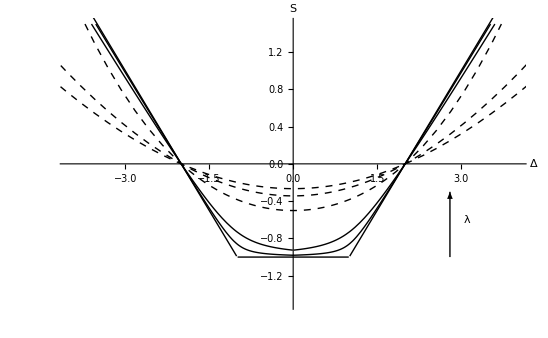

```mathematica
bfklplot=Show[
Plot[Evaluate@Table[bfkl,{λ,12,75,25}],{δ,-6,6},PlotRange->{{-4,4},{-1.5,1.5}}, PlotStyle->{{Dashed,Black}},
AxesLabel->{"Δ","S"},AxesStyle->{{Arrowheads[{0,0.02}]},{Arrowheads[{0,0.02}]}}],
Plot[{x-2 If[x>1.01,1],-x-2 If[x<-1.01,1],-1 If[x^2<0.986,1]},{x,-4,4},PlotStyle->{{Black,Thick}}],
Show[{ParametricPlot[{S+2+8 g^2 HarmonicNumber[S],S}/.g->1/20,{S,-0.9805,1.5},PlotStyle->Black],ParametricPlot[{-(S+2+8 g^2 HarmonicNumber[S]),S}/.g->1/20,{S,-0.9805,1.5},PlotStyle->Black]},PlotRange->{{-4,4},{-1.5,1.5}}, PlotStyle->Red],
Show[{ParametricPlot[{S+2+8 g^2 HarmonicNumber[S],S}/.g->1/10,{S,-0.9257,1.5},PlotStyle->Black],ParametricPlot[{-(S+2+8 g^2 HarmonicNumber[S]),S}/.g->1/10,{S,-0.9257,1.5},PlotStyle->Black]},PlotRange->{{-4,4},{-1.5,1.5}}, PlotStyle->Red],
Show[Graphics[{Arrowheads[0.02],Arrow[{{2.8,-1},{2.8,-0.3}}]}]], Show[Graphics[{Text["λ",{3.1,-0.6}]}]]
(*Show[Graphics[{Arrowheads[0.015],
Arrow[{{2.3,-0.5},{2,-0.5},{1,-0.198692}}],
Arrow[{{2.3,-0.65},{2,-0.65},{0.8,-0.287532}}],
Arrow[{{2.3,-0.8},{2,-0.8},{0.6,-0.459294}}],
Arrow[{{2.3,-0.95},{2,-0.95},{0.9,-0.77312}}],
Arrow[{{2.3,-1.1},{2,-1.1},{0.8,-0.9272}}]
}]],
Show[Graphics[{Text["g = 0.63",{2.7,-0.5}],Text["g = 0.48",{2.7,-0.65}],Text["g = 0.28",{2.7,-0.8}],Text["g = 0.10",{2.7,-0.95}],Text["g = 0.05",{2.7,-1.1}]}]]*)
]
```

Pade fit for the intercept:

```mathematica
weakpowers=2;
strongpowers=3;
```

```mathematica
istrong=Table[SeriesCoefficient[intercept,{λ,∞,i/2}],{i,0,strongpowers}]
```

{2,-2,-1,1/4}

```mathematica
iweak=Table[SeriesCoefficient[j[0]/.g->(√λ)/(4Pi),{λ,0,i}]//N//Chop//Rationalize,{i,0,weakpowers}]
```

{1,0.0702305,-0.00337171}

```mathematica
y= D[Log[BesselI[S,x]],x]-S/.x->√λ/.S->2;
ylarge=Series[Series[Series[y,{λ,∞,6}]/.Exp[a_ √λ]->LL^a//Normal,{LL,∞,0}],{λ,∞,6}]//Normal;
```

```mathematica
Block[{PW=3},pade=(Plus@@Table[a[i] z^i,{i,0,PW}])/(Plus@@Table[b[i] z^i,{i,0,PW}])/.a[PW]->1/.b[PW]->1];
```

```mathematica
pweak=Table[SeriesCoefficient[pade/.z->y,{λ,0,i}],{i,0,weakpowers}];
```

```mathematica
pstrong=Table[SeriesCoefficient[pade/.z->ylarge,{λ,∞,i/2}],{i,0,strongpowers}];
```

```mathematica
sln=Block[{vars,expr},
expr=Thread[Equal[istrong,pstrong]]~Join~Thread[Equal[iweak,pweak]];
vars=Cases[expr,a[_]|b[_],∞]//Union;
Solve[expr,vars][[1]]//Simplify//Quiet
];
```

```mathematica
padefit=pade/.sln//Simplify
```

(z^3+3.63402 z^2+4.26822 z+1.62791)/(z^3+3.25079 z^2+3.50796 z+1.25402)

Now compare: fit vs. exact vs. Lipatov:

```mathematica
Series[padefit/.z->ylarge,{λ,∞,5}]//Chop//Simplify
```

2.-2. √(1/λ)-1./λ+0.25 (1/λ)^(3/2)+729.244/λ^2-3195.7 (1/λ)^(5/2)+20031.1/λ^3-227831. (1/λ)^(7/2)+(1.72628×10^6)/λ^4-1.32796×10^7 (1/λ)^(9/2)+(1.105×10^8)/λ^5+O((1/λ)^(11/2))

```mathematica
Series[intercept,{λ,∞,4}]//N
```

2.-2. √(1/λ)-1/λ+0.25 (1/λ)^(3/2)+9.21234/λ^2+27.2776 (1/λ)^(5/2)+60.849/λ^3+O((1/λ)^(9/2))

```mathematica
2-Series[2/λ^(1/2)(1+1/(2 λ^(1/2))-1/(8λ)-(1+3Zeta[3])1/λ^(3/2)+(2 a[1,2]-145/128-9/2 Zeta[3])1/λ^2),{λ,∞,4}]/.a[1,2]->−22.2348//N
```

2.-2. √(1/λ)-1/λ+0.25 (1/λ)^(3/2)+9.21234/λ^2+102.023 (1/λ)^(5/2)+O((1/λ)^(9/2))

Plot the intercept:

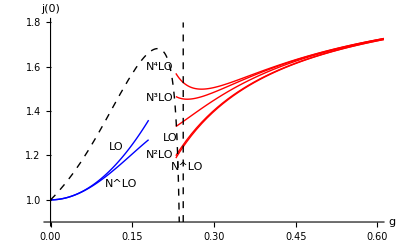

```mathematica
interceptplot=Block[{range={{0,0.6},{0.9,1.8}}},Show[
Plot[Evaluate[Table[Series[j[0],{g,0,2i}]//Normal,{i,1,2}]],{g,0,0.18},PlotRange->range,PlotStyle->Blue,
AxesLabel->{"g","j(0)"},AxesStyle->{{Arrowheads[{0,0.02}]},{Arrowheads[{0,0.02}]}}],
Table[Plot[Evaluate[2+bfkl/.δ->0/.λ->16 π^2 g^2//Series[#,{g,∞,i}]&//Normal],{g,0.23,0.7},PlotRange->range,PlotStyle->{Red}],{i,2,6}],
(*Plot[2+-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 Zeta[3]+2)/λ^2+(1/λ)^(5/2) (-4 a[1,2]+9 Zeta[3]+145/64)/.λ->16 π^2 g^2/.a[1,2]->-22,{g,0.2,0.6},PlotRange->range,PlotStyle->Green],*)
Plot[padefit/.z->y/.λ->16 π^2 g^2,{g,0.0,0.7},PlotRange->range,PlotStyle->{Black,Dashed}],
Graphics[Text["N^LO",{0.13,1.07}]],Graphics[Text["LO",{0.12,1.24}]],
Graphics[Text["LO",{0.22,1.28}]],Graphics[Text["N^LO",{0.25,1.15}]],Graphics[Text["N^2LO",{0.20,1.2}]],Graphics[Text["N^3LO",{0.20,1.46}]],Graphics[Text["N^4LO",{0.20,1.6}]]
]]
```

Lipatov’s estimation of a[1,2]:

```mathematica
ww=et1 λ+et2 λ^2+et3 λ^3;
etrep={et1->1/4(4Log[2])/π^2,et2->-0.01350443480483234/4};
Series[ww/.etrep,{λ,0,2}]//N//Chop
```

0.0702305 λ-0.00337611 λ^2+O(λ^3)

```mathematica
Series[(interceptweak-1),{λ,0,2}]//N//Chop
```

0.280922 λ-0.0135044 λ^2+O(λ^3)

```mathematica
ws=1-2/(√λ)(1+tt1/(√λ)+tt2/λ+tt3/λ^(3/2)+tt4/λ^2);
ttrep={tt1->1/2 ,tt2->(-1/8),tt3->(-1-3Zeta[3]),tt4->2a12-145/128-9/2 Zeta[3]};
Series[ws/.ttrep,{λ,∞,2}]
```

1-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 3+2)/λ^2+O((1/λ)^(5/2))

```mathematica
Series[intercept-1,{λ,∞,2}]
```

1-2 √(1/λ)-1/λ+1/4 (1/λ)^(3/2)+(6 3+2)/λ^2+O((1/λ)^(5/2))

```mathematica
CompareSeries[srs1_, srs2_] := Thread[srs1[[3]] == srs2[[3]]]
```

```mathematica
t0=(2w)/(1-w^2);
```

```mathematica
Series[t0/.w->ww,{λ,0,3}]
Series[e1 λ+e2 λ^2+e3 λ^3,{λ,0,3}];
CompareSeries[%,%%]//Solve[#,{e1,e2,e3}]&//Last
erep=%/.etrep
```

2 et1 λ+2 et2 λ^2+2 λ^3 (et1^3+et3)+O(λ^4)

{e1→2 et1,e2→2 et2,e3→2 (et1^3+et3)}

{e1→(2 log(2))/π^2,e2→-0.00675222,e3→2 (et3+(log^3(2))/π^6)}

```mathematica
Series[t0/.w->ws,{λ,∞,2}]
Series[(√λ)/2(1-t1/(√λ)-t2/λ-t3/λ^(3/2)-t4/λ^2-t5/λ^(5/2)),{λ,∞,4}];
CompareSeries[%,%%]//Solve[#,{t1,t2,t3,t4,t5}]&//First
trep=%/.ttrep
```

(√λ)/2+1/2 (-tt1-1)+1/2 √(1/λ) (tt1^2-tt2-1)+(-tt1^3+2 tt1 tt2-tt1-tt3-1)/(2 λ)+1/2 (1/λ)^(3/2) (tt1^4-3 tt1^2 tt2+2 tt1 tt3-2 tt1+tt2^2-tt2-tt4-1)+(-tt1^5+4 tt1^3 tt2-3 tt1^2 tt3-tt1^2-3 tt1 tt2^2+2 tt1 tt4-3 tt1+2 tt2 tt3-2 tt2-tt3-1)/(2 λ^2)+O((1/λ)^(5/2))

{t1→tt1+1,t2→-tt1^2+tt2+1,t3→tt1^3-2 tt1 tt2+tt1+tt3+1,t4→-tt1^4+3 tt1^2 tt2-2 tt1 tt3+2 tt1-tt2^2+tt2+tt4+1,t5→tt1^5-4 tt1^3 tt2+3 tt1^2 tt3+tt1^2+3 tt1 tt2^2-2 tt1 tt4+3 tt1-2 tt2 tt3+2 tt2+tt3+1}

{t1→3/2,t2→5/8,t3→3/4-3 3,t4→2 a12-(3 3)/2+201/128,t5→-2 a12-(3 3)/2+7/4}

```mathematica
Series[k0/.k0->β0 λ+α0 λ^2,{λ,0,2}]
Series[k1 t+k2 t^2/.k1->β1+α1 λ/.k2->γ2 λ^-1+β2+β2 λ/.t->t0/.w->ww/.etrep,{λ,0,2}]//N//Chop
eq1=CompareSeries[%,%%]
```

β0 λ+α0 λ^2+O(λ^3)

λ (0.140461 β1+0.0197293 γ2)+λ^2 (0.140461 α1-0.00675222 β1+0.0197293 β2-0.00189685 γ2)+O(λ^3)

{0.140461 β1+0.0197293 γ2==β0,0.140461 α1-0.00675222 β1+0.0197293 β2-0.00189685 γ2==α0}

```mathematica
Series[k0/.k0->β0 λ+α0 λ^2,{λ,∞,2}]
Series[k1 t+k2 t^2/.k1->β1+α1 λ/.k2->γ2 λ^-1+β2+β2 λ/.t->t0/.w->ws/.ttrep,{λ,∞,0}]//N//Chop//Simplify//Rationalize
CompareSeries[%,%%]
```

α0 λ^2+β0 λ+O((1/λ)^3)

(β2 λ^2)/4+λ^(3/2) (α1/2-(3 β2)/4)+λ (β2/2-(3 α1)/4)+√λ (-(5 α1)/16+β1/2+1.14684 β2)+(1.42809 α1-a12 β2-(3 β1)/4-1.67809 β2+γ2/4)+O(√(1/λ))

False

## Junk

```mathematica
oneloopn2=(-1/(2𝔍)+𝔍/2)𝔖+(1/(2𝔍^3)-(12Zeta[3]+17/16)1/𝔍+(12Zeta[3]+60 Zeta[5]+27/32)𝔍)𝔖^2+(21/(4𝔍^5)+(12Zeta[3]+19/16)1/𝔍^3+(9Zeta[3]+47/32)1/𝔍-(19/4+34Zeta[3]+130Zeta[5]+280Zeta[7])𝔍)𝔖^3+(-175/(4𝔍^7)-(727/32+18Zeta[3])1/𝔍^5-(6Zeta[3]-30Zeta[5]-155/32)1/𝔍^3-(145/8 Zeta[3]+45Zeta[5]+175Zeta[7]+7419/1024)1/𝔍)𝔖^4/.𝔍->J/(√λ)/.𝔖->S/(√λ);
oneloopn2=Series[oneloopn2,{S,0,4},{λ,∞,4}]
```

S (-1/(2 J)+J/(2 λ)+O((1/λ)^5))+S^2 ((√λ)/(2 J^3)+(-(12 3)/J-17/(16 J)) √(1/λ)+(60 5 J+12 3 J+(27 J)/32) (1/λ)^(3/2)+O((1/λ)^(9/2)))+S^3 ((21 λ)/(4 J^5)+((12 3)/J^3+19/(16 J^3))+((9 3)/J+47/(32 J))/λ+(-280 7 J-130 5 J-34 3 J-(19 J)/4)/λ^2+O((1/λ)^5))+S^4 (-(175 λ^(3/2))/(4 J^7)+(-(18 3)/J^5-727/(32 J^5)) √λ+((30 5)/J^3-(6 3)/J^3+155/(32 J^3)) √(1/λ)+(-(175 7)/J-(45 5)/J-(145 3)/(8 J)-7419/(1024 J)) (1/λ)^(3/2)+O((1/λ)^(9/2)))+O(S^5)

```mathematica
ΔsqFTn2=(Series[(√(n^2 λ Normal[classical]))/.𝔍->J/(n √λ)/.𝔖->S/(n √λ)/.n->2,{S,0,6},{λ,∞,5}]+oneloopn2//Simplify[#,J>0]&)^2//Series[#,{S,0,6},{λ,∞,5}]&
```

J^2+S (4 √λ-1+1/2 J^2 √(1/λ)+J^2/λ-1/32 J^4 (1/λ)^(3/2)+1/256 J^6 (1/λ)^(5/2)-(5 J^8 (1/λ)^(7/2))/8192+(7 J^10 (1/λ)^(9/2))/65536+O((1/λ)^5))+S^2 (-(√λ)/J^2+(3/2+1/(4 J^2))-3/8 (1+64 3) √(1/λ)+(-J^2/8-1/2)/λ+1/64 (7680 5 J^2+1536 3 J^2+125 J^2) (1/λ)^(3/2)+(J^4+8 J^2)/(32 λ^2)-9/512 J^4 (1/λ)^(5/2)-J^6/(128 λ^3)+(37 J^6 (1/λ)^(7/2))/16384+J^8/(512 λ^4)+O((1/λ)^(9/2)))+S^3 ((29 λ)/(2 J^4)-(√λ)/(2 J^4)+(-31-192 3)/(8 J^2)+((-3 J^2+192 3+25) √(1/λ))/(16 J^2)+(389+3840 3+15360 5)/(64 λ)+1/128 (13 J^2-7680 5-3072 3-244) (1/λ)^(3/2)+(-143360 7 J^2-58880 5 J^2-15776 3 J^2-2335 J^2)/(256 λ^2)+(J (60 5 J+12 3 J+(27 J)/32)-(85 J^4)/2048) (1/λ)^(5/2)+(-30720 5 J^4-6912 3 J^4-185 J^4)/(16384 λ^3)+(245 J^6 (1/λ)^(7/2))/16384+O((1/λ)^4))+S^4 (-(145 λ^(3/2))/(2 J^6)-(5 λ)/J^6+((-473+960 3) √λ)/(16 J^4)-(3 (-1+8 3))/J^4+((1547-3072 3-23040 5) √(1/λ))/(128 J^2)+(31 J^2+15360 5+36864 3^2+10368 3+433)/(256 J^2 λ)+((-33083-164480 3-593920 5-1505280 7) (1/λ)^(3/2))/1024+(-53 J^2+143360 7-737280 3 5+1280 5-147456 3^2-1408 3+2266)/(512 λ^2)+((-4587520 7 J^2-2375680 5 J^2-626176 3 J^2-81925 J^2) (1/λ)^(5/2))/32768+((241 J^4)/4096-1/4 (19+136 3+520 5+1120 7) J^2+(60 5 J+12 3 J+(27 J)/32)^2)/λ^3+O((1/λ)^(7/2)))+O(S^5)

```mathematica
Δsqn2=J^2+S(∑_(i=1)^7 A[i] μ^((2-i)/2))+S^2(∑_(i=1)^8 B[i] μ^((1-i)/2))+S^3(∑_(i=1)^8 CC[i] μ^((0-i)/2))+S^4(∑_(i=1)^8 DD[i] μ^((-1-i)/2))+S^5(∑_(i=1)^8 EE[i] μ^((-2-i)/2))/.μ->n^2 λ/.n->2//Series[#,{S,0,5},{λ,∞,2}]&//Simplify[#,n>0]&
```

J^2+S (2 A(1) √λ+A(2)+1/2 A(3) √(1/λ)+(A(4))/(4 λ)+1/8 A(5) (1/λ)^(3/2)+(A(6))/(16 λ^2)+O((1/λ)^(5/2)))+S^2 (B(1)+1/2 B(2) √(1/λ)+(B(3))/(4 λ)+1/8 B(4) (1/λ)^(3/2)+(B(5))/(16 λ^2)+O((1/λ)^(5/2)))+S^3 (1/2 CC(1) √(1/λ)+(CC(2))/(4 λ)+1/8 CC(3) (1/λ)^(3/2)+(CC(4))/(16 λ^2)+O((1/λ)^(5/2)))+S^4 ((DD(1))/(4 λ)+1/8 DD(2) (1/λ)^(3/2)+(DD(3))/(16 λ^2)+1/32 DD(4) (1/λ)^(5/2)+O((1/λ)^3))+S^5 (1/8 EE(1) (1/λ)^(3/2)+(EE(2))/(16 λ^2)+O((1/λ)^(5/2)))+O(S^6)

```mathematica
Series[√Δsqn2,{S,0,2},{λ,∞,4}]//Simplify[#,J>0]&
```

J+S ((A(1) √λ)/J+(A(2))/(2 J)+(A(3) √(1/λ))/(4 J)+(A(4))/(8 J λ)+(A(5) (1/λ)^(3/2))/(16 J)+(A(6))/(32 J λ^2)+O((1/λ)^(5/2)))+S^2 (-((A(1))^2 λ)/(2 J^3)-((A(1) A(2)) √λ)/(2 J^3)-(-4 B(1) J^2+(A(2))^2+2 A(1) A(3))/(8 J^3)-((-2 B(2) J^2+A(2) A(3)+A(1) A(4)) √(1/λ))/(8 J^3)-(-4 B(3) J^2+(A(3))^2+2 A(2) A(4)+2 A(1) A(5))/(32 J^3 λ)-((-2 B(4) J^2+A(3) A(4)+A(2) A(5)+A(1) A(6)) (1/λ)^(3/2))/(32 J^3)+O((1/λ)^2))+O(S^3)

```mathematica
n2coeffs={A[i_]:>(2^(2-i)A[i]/.As)};
```

```mathematica
Series[SeriesCoefficient[√(Δsqn2//Normal)/.λ->(4π g)^2,{S,0,2}],{g,∞,3}]/.J->Zeta[3]/.Zeta[3]->J/.n2coeffs/.J->2//Simplify
```

-16 π^2 g^2+π g+1/4 (B(1)-1)+(64 B(2)-15)/(2048 π g)+(64 B(3)-15)/(16384 π^2 g^2)+(8 B(4)-405/512)/(16384 π^3 g^3)+O((1/g)^4)

```mathematica
Solve[(1/4 (B[1]-1))==17/8,B[1]]
```

{{B(1)→19/2}}

```mathematica
Δsqn2=J^2+S(∑_(i=1)^7 A[i] μ^((2-i)/2))+S^2(∑_(i=1)^8 B[i] μ^((1-i)/2))+S^3(CC[-2]μ+∑_(i=1)^8 CC[i] μ^((0-i)/2))+S^4(DD[-4] μ^(3/2)+DD[-2] √μ+DD[0]/√μ+∑_(i=1)^8 DD[i] μ^((-1-i)/2))+S^5(∑_(i=1)^8 EE[i] μ^((-2-i)/2))/.μ->n^2 λ/.n->2//Series[#,{S,0,5},{λ,∞,2}]&//Simplify[#,n>0]&//Normal
```

(1/16 A(6) S+1/16 B(5) S^2+1/16 CC(4) S^3+1/16 DD(3) S^4+1/16 EE(2) S^5)/λ^2+(1/λ)^(3/2) (1/8 A(5) S+1/8 B(4) S^2+1/8 CC(3) S^3+1/8 DD(2) S^4+1/8 EE(1) S^5)+√(1/λ) (1/2 A(3) S+1/2 B(2) S^2+1/2 CC(1) S^3+1/2 DD(0) S^4)+(1/4 A(4) S+1/4 B(3) S^2+1/4 CC(2) S^3+1/4 DD(1) S^4)/λ+(2 A(1) S+2 DD(-2) S^4)/(√(1/λ))+A(2) S+B(1) S^2+4 CC(-2) λ S^3+(8 DD(-4) S^4)/(1/λ)^(3/2)+J^2

```mathematica
StoE=(δ^2-4)∑_(i=-3)^-3 1/λ^(i/2)∑_(j=0)^3 α[i,j] δ^j;
```

```mathematica
vars=Cases[StoE,α[_,_],∞]//Union;
```

```mathematica
eqns=(Series[(Δsqn2/.S->StoE)-δ^2/.λ->ll^2,{ll,∞,1},{δ,0,1}]==0)//LogicalExpand//Simplify
```

2 J^2==A(5) α(-3,0)∧A(4) α(-3,0)==0∧A(6) α(-3,0)==0∧CC(2) α(-3,0)==0∧DD(-4) α(-3,0)==0∧DD(-2) α(-3,0)==0∧DD(1) α(-3,0)==0∧DD(2) α(-3,0)==0∧EE(1) α(-3,0)==0∧A(4) α(-3,1)==0∧A(6) α(-3,1)==0∧A(5) α(-3,1)==0∧B(3) (α(-3,0))^2==2 A(1) α(-3,0)∧B(4) (α(-3,0))^2==2 A(2) α(-3,0)∧B(5) (α(-3,0))^2==2 A(3) α(-3,0)∧CC(3) (α(-3,0))^2==2 B(1) α(-3,0)∧CC(4) (α(-3,0))^2==2 B(2) α(-3,0)∧DD(3) (α(-3,0))^2==2 CC(1) α(-3,0)∧4 CC(-2) α(-3,0)+EE(2) (α(-3,0))^3==2 DD(0) (α(-3,0))^2∧α(-3,1) (A(1)-B(3) α(-3,0))==0∧α(-3,1) (A(2)-B(4) α(-3,0))==0∧α(-3,1) (A(3)-B(5) α(-3,0))==0∧α(-3,0) α(-3,1) (3 CC(3) α(-3,0)-4 B(1))==0∧α(-3,0) α(-3,1) (3 CC(4) α(-3,0)-4 B(2))==0∧α(-3,0) α(-3,1) (2 DD(3) α(-3,0)-3 CC(1))==0∧α(-3,0) α(-3,1) (α(-3,0) (5 EE(2) α(-3,0)-8 DD(0))+12 CC(-2))==0

```mathematica
Solve[eqns,vars]
```

{}

```mathematica
S[l_]:=∑_(i=-l)^l ∑_(j=0)^10 a[i,j] λ^(-i/2)δ^j
```

```mathematica
S[1]
```

δ^10 √λ a(-1,10)+(δ^10 a(1,10))/(√λ)+δ^10 a(0,10)+δ^9 √λ a(-1,9)+(δ^9 a(1,9))/(√λ)+δ^9 a(0,9)+δ^8 √λ a(-1,8)+(δ^8 a(1,8))/(√λ)+δ^8 a(0,8)+δ^7 √λ a(-1,7)+(δ^7 a(1,7))/(√λ)+δ^7 a(0,7)+δ^6 √λ a(-1,6)+(δ^6 a(1,6))/(√λ)+δ^6 a(0,6)+δ^5 √λ a(-1,5)+(δ^5 a(1,5))/(√λ)+δ^5 a(0,5)+δ^4 √λ a(-1,4)+(δ^4 a(1,4))/(√λ)+δ^4 a(0,4)+δ^3 √λ a(-1,3)+(δ^3 a(1,3))/(√λ)+δ^3 a(0,3)+δ^2 √λ a(-1,2)+(δ^2 a(1,2))/(√λ)+δ^2 a(0,2)+δ √λ a(-1,1)+(δ a(1,1))/(√λ)+δ a(0,1)+√λ a(-1,0)+(a(1,0))/(√λ)+a(0,0)

```mathematica
eqns=Series[Δsqn2-δ^2/.S->S[1],{δ,0,2},{λ,∞,-3}]==0//LogicalExpand//Simplify
```

$Aborted

```mathematica
vars=Cases[eqns,a[_,_],∞]//Union;
Solve[eqns,vars]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a(-3,0)→0,a(-3,1)→0},{a(-3,0)→0,a(0,0)→0}}

```mathematica
δ[S_,λ_]=√Δsqn2/.coeffs/.DD[-4]->-78/J^6/.DD[-2]->-36/J^4/.DD[0]->21/(2 J^2)/.CC[-2]->12/J^4/.b3/.J->2/.EE[_]->0/.B[_]->0/.DD[_]->0/.CC[_]->0
```

√(-(39 S^4)/(4 (1/λ)^(3/2))+(4 S-(9 S^4)/2)/(√(1/λ))+(1/λ)^(3/2) ((S^4 (-5520 3-5120 5-3640 7+901))/4096+(135 S)/512)+3 λ S^3+(3 S^2)/2+√(1/λ) ((21 S^4)/16-(3 S^3)/16-3/16 S^2 (8 3-1)+(15 S)/8)+((31 S^4)/256+1/64 S^3 (60 3+60 5-17)+1/4 S^2 (-(9 3)/2-27/16)+(15 S)/16)/λ-(45 S)/(256 λ^2)-S+4)

```mathematica
S[Δ_,λ_]:=S/.FindRoot[δ[S,λ]==Δ,{S,0}]//Chop
```

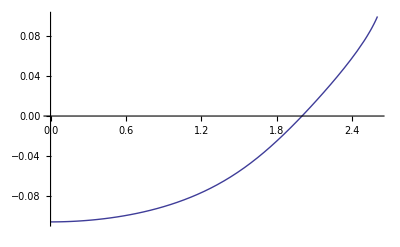

```mathematica
Plot[S[d,60],{d,0,2.6}]
```

```mathematica
√Δsqn2/.coeffs/.DD[-4]->-78/J^6/.DD[-2]->-36/J^4/.DD[0]->21/(2 J^2)/.CC[-2]->12/J^4/.b3/.J->2/.EE[_]->0/.B[_]->0/.DD[_]->0/.CC[_]->0
```

√(-(39 S^4)/(4 (1/λ)^(3/2))+(4 S-(9 S^4)/2)/(√(1/λ))+(1/λ)^(3/2) ((S^4 (-5520 3-5120 5-3640 7+901))/4096+(135 S)/512)+3 λ S^3+(3 S^2)/2+√(1/λ) ((21 S^4)/16-(3 S^3)/16-3/16 S^2 (8 3-1)+(15 S)/8)+((31 S^4)/256+1/64 S^3 (60 3+60 5-17)+1/4 S^2 (-(9 3)/2-27/16)+(15 S)/16)/λ-(45 S)/(256 λ^2)-S+4)

```mathematica
vars=Cases[StoE,α[_,_],∞]//Union;
sln=(Series[(Δsqn2/.S->StoE)-δ^2/.λ->ll^2,{ll,∞,2},{δ,0,2}])==0//LogicalExpand//Simplify//Solve[#,vars]&//Last//Quiet;
```

```mathematica
sln
```

Last[{}]

What coefficients does the intercept depend on ?

```mathematica
Series[StoE/.sln/.δ->0,{λ,∞,3}]/.As/.b1/.b2/.c1/.J->2//Simplify
```

ReplaceAll::reps: TraditionalForm`{Last[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0/.Last[{}])-4 √(1/λ) (α(1,0) ReplaceAll^(1,0)(0,Last[{}]))+(8 (α(1,0))^2 ReplaceAll^(2,0)(0,Last[{}])-4 α(2,0) ReplaceAll^(1,0)(0,Last[{}]))/λ+(1/λ)^(3/2) (-32/3 (α(1,0))^3 ReplaceAll^(3,0)(0,Last[{}])+16 α(2,0) α(1,0) ReplaceAll^(2,0)(0,Last[{}])-4 α(3,0) ReplaceAll^(1,0)(0,Last[{}]))+(32/3 (α(1,0))^4 ReplaceAll^(4,0)(0,Last[{}])-32 α(2,0) (α(1,0))^2 ReplaceAll^(3,0)(0,Last[{}])-4 α(4,0) ReplaceAll^(1,0)(0,Last[{}])+8 ((α(2,0))^2+2 α(1,0) α(3,0)) ReplaceAll^(2,0)(0,Last[{}]))/λ^2-16/15 (1/λ)^(5/2) (2 α(1,0) (4 (α(1,0))^2 ((α(1,0))^2 ReplaceAll^(5,0)(0,Last[{}])-5 α(2,0) ReplaceAll^(4,0)(0,Last[{}]))+15 ((α(2,0))^2+α(1,0) α(3,0)) ReplaceAll^(3,0)(0,Last[{}]))-15 (α(2,0) α(3,0)+α(1,0) α(4,0)) ReplaceAll^(2,0)(0,Last[{}]))+(8 (45 ((α(3,0))^2+2 α(2,0) α(4,0)) ReplaceAll^(2,0)(0,Last[{}])-4 (15 ((α(2,0))^3+6 α(1,0) α(3,0) α(2,0)+3 (α(1,0))^2 α(4,0)) ReplaceAll^(3,0)(0,Last[{}])-2 (α(1,0))^2 (4 (α(1,0))^4 ReplaceAll^(6,0)(0,Last[{}])-30 α(2,0) (α(1,0))^2 ReplaceAll^(5,0)(0,Last[{}])+15 (3 (α(2,0))^2+2 α(1,0) α(3,0)) ReplaceAll^(4,0)(0,Last[{}])))))/(45 λ^3)+O((1/λ)^(7/2))

```mathematica
Δsqn2
```

(1/16 A(6) S+1/16 B(5) S^2+1/16 CC(4) S^3+1/16 DD(3) S^4+1/16 EE(2) S^5)/λ^2+(1/λ)^(3/2) (1/8 A(5) S+1/8 B(4) S^2+1/8 CC(3) S^3+1/8 DD(2) S^4+1/8 EE(1) S^5)+√(1/λ) (1/2 A(3) S+1/2 B(2) S^2+1/2 CC(1) S^3+1/2 DD(0) S^4)+(1/4 A(4) S+1/4 B(3) S^2+1/4 CC(2) S^3+1/4 DD(1) S^4)/λ+(2 A(1) S+2 DD(-2) S^4)/(√(1/λ))+A(2) S+B(1) S^2+4 CC(-2) λ S^3+(8 DD(-4) S^4)/(1/λ)^(3/2)+J^2

```mathematica
Δabc=√Δsqn2/.J->2;
```

```mathematica
Series[Δabc,{S,0,3}]
```

2+(S (16 A(2) λ^2+4 A(4) λ+(32 A(1))/(1/λ)^(5/2)+(8 A(3))/(1/λ)^(3/2)+(2 A(5))/(√(1/λ))+A(6)))/(64 λ^2)+S^2 ((16 B(1) λ^2+4 B(3) λ+(8 B(2))/(1/λ)^(3/2)+(2 B(4))/(√(1/λ))+B(5))/(64 λ^2)-1/64 ((A(6))/(16 λ^2)+1/8 A(5) (1/λ)^(3/2)+1/2 A(3) √(1/λ)+(A(4))/(4 λ)+(2 A(1))/(√(1/λ))+A(2))^2)+2/3 S^3 ((3 (64 CC(-2) λ^3+4 CC(2) λ+(8 CC(1))/(1/λ)^(3/2)+(2 CC(3))/(√(1/λ))+CC(4)))/(128 λ^2)-3/16 ((A(6))/(16 λ^2)+1/8 A(5) (1/λ)^(3/2)+1/2 A(3) √(1/λ)+(A(4))/(4 λ)+(2 A(1))/(√(1/λ))+A(2)) ((16 B(1) λ^2+4 B(3) λ+(8 B(2))/(1/λ)^(3/2)+(2 B(4))/(√(1/λ))+B(5))/(64 λ^2)-1/64 ((A(6))/(16 λ^2)+1/8 A(5) (1/λ)^(3/2)+1/2 A(3) √(1/λ)+(A(4))/(4 λ)+(2 A(1))/(√(1/λ))+A(2))^2))+O(S^4)

```mathematica
S[l_,d_]:=∑_(i=1)^l ∑_(j=0)^d a[l,d] λ^(-i/2)δ^j
```

```mathematica
Normal@Series[SeriesCoefficient[Δabc/.S->S[1,1],{δ,0,1}],{λ,∞,0}]==1//Solve
```

{{a(1,1)→(1+√5)/(A(1))}}

```mathematica
Series[S[1,1],{λ,∞,2},{δ,0,2}]
```

√(1/λ) (a(1,1)+a(1,1) δ+O(δ^3))+O((1/λ)^(5/2))

```mathematica
Series[S[1,1]/.δ->Δabc,{λ,∞,0},{S,0,1}]
```

λ^(1/4) O(S^2)+O((1/λ)^(1/4))

```mathematica
Series[Δabc,{S,0,1},{λ,∞,5}]
```

2+S (1/2 A(1) √λ+(A(2))/4+1/8 A(3) √(1/λ)+(A(4))/(16 λ)+1/32 A(5) (1/λ)^(3/2)+(A(6))/(64 λ^2)+O((1/λ)^(11/2)))+O(S^2)

```mathematica
s[δ_]:=1/(√λ)
```

```mathematica
Series[S/.Solve[δ==Normal@Series[Δabc,{S,0,1},{λ,∞,0}],S][[1]],{λ,∞,1}]
```

(2 (δ-2) √(1/λ))/(A(1))-(A(2) (δ-2))/((A(1))^2 λ)+O((1/λ)^(3/2))

```mathematica
S[δ_]:=
```

```mathematica
Δabc
```

√((1/16 A(6) S+1/16 B(5) S^2+1/16 CC(4) S^3+1/16 DD(3) S^4+1/16 EE(2) S^5)/λ^2+(1/λ)^(3/2) (1/8 A(5) S+1/8 B(4) S^2+1/8 CC(3) S^3+1/8 DD(2) S^4+1/8 EE(1) S^5)+√(1/λ) (1/2 A(3) S+1/2 B(2) S^2+1/2 CC(1) S^3+1/2 DD(0) S^4)+(1/4 A(4) S+1/4 B(3) S^2+1/4 CC(2) S^3+1/4 DD(1) S^4)/λ+(2 A(1) S+2 DD(-2) S^4)/(√(1/λ))+A(2) S+B(1) S^2+4 CC(-2) λ S^3+(8 DD(-4) S^4)/(1/λ)^(3/2)+J^2)

```mathematica
Series[,{λ,∞,0}]//Simplify[#,J>0]&
```

2 √2 λ^(3/4) √(DD(-4) S^4)+(CC(-2) λ^(1/4) S^3)/(√2 √(DD(-4) S^4))+O((1/λ)^(1/4))

```mathematica
classical
```

((3 (𝔍^2+6) 𝔍^2+31) 𝔖^4)/(64 (𝔍^2+1)^4)+((-𝔍^2-3) 𝔖^3)/(8 (𝔍^2+1)^(5/2))+(1/(2 𝔍^2+2)+1) 𝔖^2+2 √(𝔍^2+1) 𝔖+𝔍^2

```mathematica
Series[n^2(√λ)^2 classical/.𝔍->J/(n √λ)/.𝔖->S/(n √λ),{S,0,4},{λ,∞,3}]
```

J^2+S (2 n √λ+(J^2 √(1/λ))/n-(J^4 (1/λ)^(3/2))/(4 n^3)+(J^6 (1/λ)^(5/2))/(8 n^5)+O((1/λ)^(7/2)))+S^2 (3/2-J^2/(2 n^2 λ)+J^4/(2 n^4 λ^2)-J^6/(2 n^6 λ^3)+O((1/λ)^4))+S^3 (-(3 √(1/λ))/(8 n)+(13 J^2 (1/λ)^(3/2))/(16 n^3)-(85 J^4 (1/λ)^(5/2))/(64 n^5)+O((1/λ)^(7/2)))+S^4 (31/(64 n^2 λ)-(53 J^2)/(32 n^4 λ^2)+(241 J^4)/(64 n^6 λ^3)+O((1/λ)^4))+O(S^5)

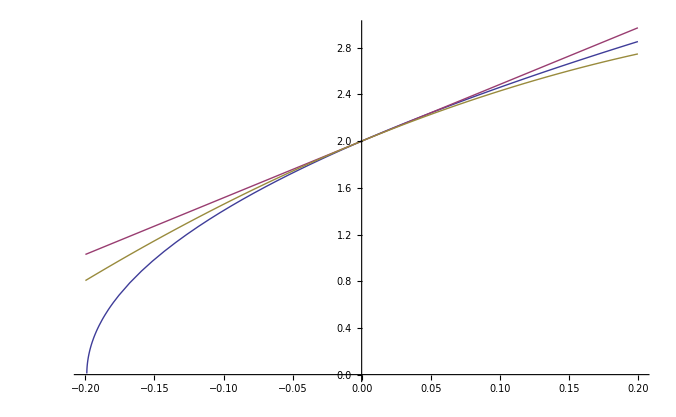

```mathematica
Block[{J=2,n=1,λ=100,range=0.2},
Plot[{
n √λ √classical/.𝔍->J/(n √λ)/.𝔖->S/(n √λ),
J+S+(n √λ)/J BesselI[J+1,n √λ]/BesselI[J,n √λ] S,
J+S+(n √λ)/J BesselI[J+1,n √λ]/BesselI[J,n √λ] S+((-π^2 g^2+(π g)/4+1/8-(96Zeta[3]+3)/(512π g))/.g->(√λ)/(4π))S^2

},{S,-range,range}]]
```

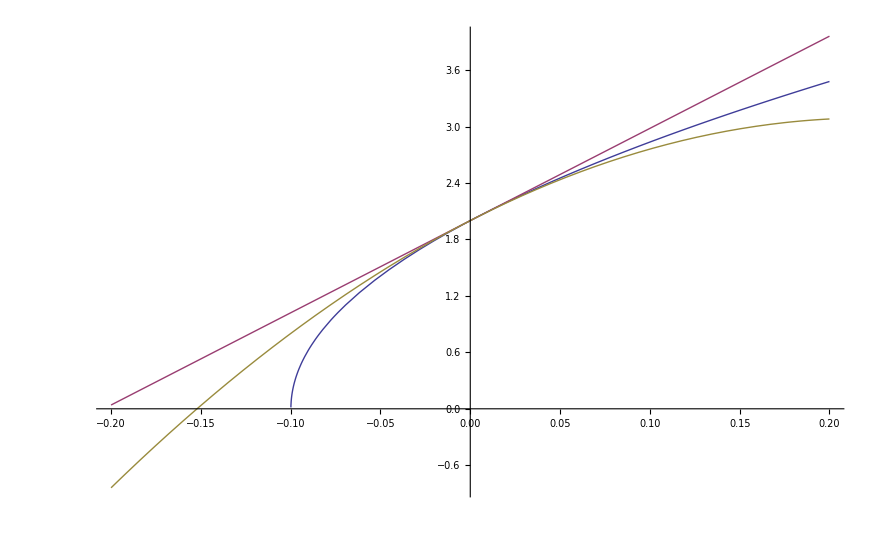

```mathematica
Block[{J=2,n=2,λ=100,range=0.2},
Plot[{
n √λ √classical/.𝔍->J/(n √λ)/.𝔖->S/(n √λ),
J+S+(n √λ)/J BesselI[J+1,n √λ]/BesselI[J,n √λ] S,
J+S+(n √λ)/J BesselI[J+1,n √λ]/BesselI[J,n √λ] S+((-4 π^2 g^2+(π g)/2+17/8-0.2958487703/g)/.g->(√λ)/(4π))S^2

},{S,-range,range}]]
```

## Junk

```mathematica
EtoS/.ll->Style[√λ,Red]
```

(J^2+O((1/(√λ))^2))+S ((√λ)/(α(1,0))-(α(2,0))/(α(1,0))^2+((α(2,0))^2-α(1,0) (α(3,1) J^2+α(3,0)))/((α(1,0))^3 √λ)+O((1/(√λ))^2))+S^2 (-(α(3,1))/(α(1,0))^3+(3 α(2,0) α(3,1)-α(1,0) α(4,1))/((α(1,0))^4 √λ)+O((1/(√λ))^2))+S^3 ((2 (α(3,1))^2)/((α(1,0))^5 √λ)+O((1/(√λ))^2))+O(S^4)

```mathematica
cf=Table[SeriesCoefficient[SeriesCoefficient[EtoS//Normal,{S,0,i}],{ll,∞,j}],{i,0,4},{j,-1,2}]
```

(0 | J^2 | 0 | 0
1/(α(1,0)) | -(α(2,0))/(α(1,0))^2 | (-α(1,0) α(3,1) J^2+(α(2,0))^2-α(1,0) α(3,0))/(α(1,0))^3 | (-(α(2,0))^3+2 α(1,0) α(3,0) α(2,0)+2 J^2 α(1,0) α(3,1) α(2,0)-(α(1,0))^2 α(4,0)-J^2 (α(1,0))^2 α(4,1))/(α(1,0))^4
0 | -(α(3,1))/(α(1,0))^3 | (3 α(2,0) α(3,1)-α(1,0) α(4,1))/(α(1,0))^4 | (3 (-2 α(3,1) (α(2,0))^2+α(1,0) α(4,1) α(2,0)+J^2 α(1,0) (α(3,1))^2+α(1,0) α(3,0) α(3,1)))/(α(1,0))^5
0 | 0 | (2 (α(3,1))^2)/(α(1,0))^5 | (4 α(3,1) α(4,1))/(α(1,0))^5-(10 α(2,0) (α(3,1))^2)/(α(1,0))^6
0 | 0 | 0 | -(5 (α(3,1))^3)/(α(1,0))^7)

```mathematica
cf2=Table[SeriesCoefficient[SeriesCoefficient[Δsq/.λ->ll^2,{S,0,i}],{ll,∞,j}],{i,0,4},{j,-1,2}]
```

(0 | J^2 | 0 | 0
A(1) | A(2) | A(3) | A(4)
0 | B(1) | B(2) | B(3)
0 | 0 | CC(1) | CC(2)
0 | 0 | 0 | DD(1))

```mathematica
sln2=Solve[cf==cf2,{A[1],A[2],A[3],A[4],B[1],B[2],B[3],CC[1],CC[2],DD[1]}][[1]]//Simplify//Collect[#,J,Simplify]&
```

{A(1)→1/(α(1,0)),A(2)→-(α(2,0))/(α(1,0))^2,A(3)→((α(2,0))^2-α(1,0) α(3,0))/(α(1,0))^3-(J^2 α(3,1))/(α(1,0))^2,A(4)→(J^2 (2 α(2,0) α(3,1)-α(1,0) α(4,1)))/(α(1,0))^3-((α(2,0))^3-2 α(1,0) α(3,0) α(2,0)+(α(1,0))^2 α(4,0))/(α(1,0))^4,B(1)→-(α(3,1))/(α(1,0))^3,B(2)→(3 α(2,0) α(3,1)-α(1,0) α(4,1))/(α(1,0))^4,B(3)→(3 (-2 α(3,1) (α(2,0))^2+α(1,0) α(4,1) α(2,0)+α(1,0) α(3,0) α(3,1)))/(α(1,0))^5+(3 J^2 (α(3,1))^2)/(α(1,0))^4,CC(1)→(2 (α(3,1))^2)/(α(1,0))^5,CC(2)→(2 α(3,1) (2 α(1,0) α(4,1)-5 α(2,0) α(3,1)))/(α(1,0))^6,DD(1)→-(5 (α(3,1))^3)/(α(1,0))^7}

```mathematica
ones={A[1],B[1],CC[1],DD[1]}/.sln2
```

{1/(α(1,0)),-(α(3,1))/(α(1,0))^3,(2 (α(3,1))^2)/(α(1,0))^5,-(5 (α(3,1))^3)/(α(1,0))^7}

```mathematica
ones=={2,3/2,-3/8,31/64}//Thread
```

{1/(α(1,0))==2,-(α(3,1))/(α(1,0))^3==3/2,(2 (α(3,1))^2)/(α(1,0))^5==-3/8,-(5 (α(3,1))^3)/(α(1,0))^7==31/64}

```mathematica
d/.Solve[S==(StoE/.α[1,0]->1/2/.α[2,0]->1/4/.α[3,0]->-1/16/.α[4,0]->-3 Zeta[3]/2-1/2/.α[3,1]->-1/16/.α[4,1]->3Zeta[3]/8-21/64/.δ^2->d),d]//Series[#,{S,0,3},{λ,∞,2}]&//Simplify
```

{(J^2+O((1/λ)^(5/2)))+(2 √λ-1+1/4 (J^2+3) √(1/λ)+((17/16-(3 3)/2) J^2+6 3+3/2)/λ+1/32 (J^4+(-34+48 3) J^2-192 3-53) (1/λ)^(3/2)+(-6 (-3+4 3) J^4+102 J^2+384 3+113)/(64 λ^2)+O((1/λ)^(5/2))) S+(1/2+(15/8-3 3) √(1/λ)+(3 (J^2+24 3-16))/(16 λ)+1/64 (-6 (-17+24 3) J^2-72 3+347) (1/λ)^(3/2)+(3 (4 J^4+3 (51-208 3+192 3^2) J^2-2304 3^2+992 3+52))/(256 λ^2)+O((1/λ)^(5/2))) S^2+((√(1/λ))/4+(2-3 3)/λ+((5 J^2)/32+9 3^2-(33 3)/4+91/64) (1/λ)^(3/2)-(5 ((-51+72 3) J^2+576 3^2-768 3+155))/(128 λ^2)+O((1/λ)^(5/2))) S^3+O(S^4),(8 λ+(-38+48 3) √λ+(397/2-480 3+288 3^2)+(-8401/8+3687 3-4392 3^2+1728 3^3) √(1/λ)+(176421/32-(51315 3)/2+45180 3^2-35424 3^3+10368 3^4)/λ+9/128 (7-8 3)^2 (-8401+29496 3-35136 3^2+13824 3^3) (1/λ)^(3/2)+(27 (-7+8 3)^3 (-8401+29496 3-35136 3^2+13824 3^3))/(512 λ^2)+O((1/λ)^(5/2)))+(-2 √λ+1+1/4 (-J^2-3) √(1/λ)+(1/16 (-17+24 3) J^2-6 3-3/2)/λ+1/32 (-J^4+(34-48 3) J^2+192 3+53) (1/λ)^(3/2)+(6 (-3+4 3) J^4-102 J^2-384 3-113)/(64 λ^2)+O((1/λ)^(5/2))) S+(-1/2+(-15/8+3 3) √(1/λ)-(3 (J^2+24 3-16))/(16 λ)+1/64 (6 (-17+24 3) J^2+72 3-347) (1/λ)^(3/2)-(3 (4 J^4+3 (51-208 3+192 3^2) J^2-2304 3^2+992 3+52))/(256 λ^2)+O((1/λ)^(5/2))) S^2+(-(√(1/λ))/4+(-2+3 3)/λ+(-(5 J^2)/32-9 3^2+(33 3)/4-91/64) (1/λ)^(3/2)+(5 ((-51+72 3) J^2+576 3^2-768 3+155))/(128 λ^2)+O((1/λ)^(5/2))) S^3+O(S^4)}

```mathematica
Δsq/.coeffs/.b3/.b4/.B[_]->0/.CC[_]->0/.DD[_]->0/.EE[_]->0
```

S^2 ((3/16 J^2 (16 3+20 5-9)-(15 5)/2-(93 3)/8-3/16)/λ^(3/2)+(-J^2/2-(9 3)/2+5/16)/λ-(3 (8 3-1))/(8 √λ)+3/2)+J^2+S ((J^2-1/4)/(√λ)+(J^2-1/4)/λ+(-16 J^4+104 J^2-25)/(64 λ^(3/2))+(-J^4+(7 J^2)/2-13/16)/λ^2+(64 J^6-1840 J^4+4748 J^2-1073)/(512 λ^(5/2))+2 √λ-1)+S^4 (31/(64 λ)+(-5520 3-5120 5-3640 7+901)/(512 λ^(3/2)))+S^3 ((60 3+60 5-17)/(16 λ)-3/(8 √λ))

```mathematica
EtoS=d/.Solve[PowerExpand[StoE==S/.δ->√d/.λ->ll^2],d][[1]]//Series[#,{S,0,4},{ll,∞,2}]&//PowerExpand//Simplify
```

(J^2+O((1/ll)^3))+S (ll/(α(1,0))-(α(2,0))/(α(1,0))^2+((α(2,0))^2-α(1,0) (α(3,1) J^2+α(3,0)))/((α(1,0))^3 ll)-((α(2,0))^3-2 α(1,0) (α(3,1) J^2+α(3,0)) α(2,0)+(α(1,0))^2 (α(4,1) J^2+α(4,0)))/((α(1,0))^4 ll^2)+O((1/ll)^3))+S^2 (-(α(3,1))/(α(1,0))^3+(3 α(2,0) α(3,1)-α(1,0) α(4,1))/((α(1,0))^4 ll)+(3 (-2 α(3,1) (α(2,0))^2+α(1,0) α(4,1) α(2,0)+α(1,0) α(3,1) (α(3,1) J^2+α(3,0))))/((α(1,0))^5 ll^2)+O((1/ll)^3))+S^3 ((2 (α(3,1))^2)/((α(1,0))^5 ll)+(2 α(3,1) (2 α(1,0) α(4,1)-5 α(2,0) α(3,1)))/((α(1,0))^6 ll^2)+O((1/ll)^3))+S^4 (-(5 (α(3,1))^3)/((α(1,0))^7 ll^2)+O((1/ll)^3))+O(S^5)